Here it is built a data base with all cases form March 2020 to August 2020

## Functions

```mathematica
Clear[toDataObject]
```

```mathematica
toDataObject["NotFound"]:=""(*se pone 10 para que la resta con el control de -10 e identificar esto como la barra de los  casos sin fecha. IGUAL NO IMPORTA PORQUE EL HISTOGRAMA NO GRAFICA LOS STRINGS*)
toDataObject[date_]:=DateObject[date]
```

```mathematica
(* LA SALIDA EN FORMA DE DateObject ES IMPORTANTE PARA HACER LAS RESTAS RESPECTIVAS DE FECHAS*)
```

```mathematica
Clear[adHospital,fHospToCR,fHospToF,fHospToUCI,adUCI,fUCIToCR,fUCIToF,fUCIToH]
```

```mathematica
adHospital[caso_]:=FirstCase[caso,{_,x_}/;StringMatchQ[x,"hospital"]] [[1]]//toDataObject(* To indentify the admission to Hospital*)
```

```mathematica
fHospToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to casa or recuperation*)
```

```mathematica
fHospToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&StringMatchQ[y,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject (* To indentify the discharge from Hospital and do dead*)
```

```mathematica
fHospToUCI[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&StringMatchQ[y,"hospital UCI"]] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to UCI *)
```

```mathematica
adUCI[caso_]:=FirstCase[caso,{_,x_}/;StringMatchQ[x,"hospital UCI"]] [[1]]//toDataObject(* To indentify the admission to UCI*)
```

```mathematica
fUCIToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to casa or recuperation*)
```

```mathematica
fUCIToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&StringMatchQ[y,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and do dead*)
```

```mathematica
fUCIToH[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&StringMatchQ[y,"hospital"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to hospital*)
```

```mathematica
(*Eliminamos los casos de H a Outcome una vez pasaron por UCI????????*)
```

## Using the first matrices

### Splitting cases without and with admission to Hospital or UCI

```mathematica
masterM1=Import["/home/lina/Documents/datos_INS/masterM15-2020.m"];
```

```mathematica
casesHospUCI=Import["/home/lina/Documents/datos_INS/masterM15_2020HospUCI.m"];
```

```mathematica
casesHospUCIID=ToExpression[StringDrop[#,4]]&/@casesHospUCI[[All,1]]; (* Este es el ID de los casos que entran al Hosp y/o ICU*)
```

```mathematica
casesNOHospUCIID=Complement[ToExpression[StringDrop[#,4]]&/@masterM1[[1,2;;]],casesHospUCIID]; (* Este es el ID de los casos que NO entran al Hosp y/o ICU*)
```

```mathematica
Length/@{masterM1[[1,2;;]],Join[casesNOHospUCIID,casesHospUCIID]}
```

{1048536,1048536}

```mathematica
masterM=Map[Transpose[{masterM1[[All,1]],#}]&,casesHospUCI];(*Casos que entran al Hospital o UCI con fechas para las funcionesn*)
```

```mathematica
masterM[[1]]
```

{{fecha,caso2},{2020-03-15,hospital},{2020-03-16,hospital},{2020-03-17,hospital},{2020-03-18,hospital},{2020-03-19,hospital},{2020-03-20,hospital},{2020-03-21,hospital},{2020-03-22,hospital},{2020-03-23,recuperado},{2020-03-24,recuperado},{2020-03-25,recuperado},{2020-03-26,recuperado},{2020-03-27,recuperado},{2020-03-28,casa},{2020-03-29,recuperado},{2020-03-30,recuperado},{2020-03-31,recuperado},{2020-04-01,recuperado},{2020-04-02,recuperado},{2020-04-03,recuperado},{2020-04-04,recuperado},{2020-04-05,recuperado},{2020-04-06,casa},{2020-04-07,casa},{2020-04-08,recuperado},{2020-04-09,casa},{2020-04-10,casa},{2020-04-12,recuperado},{2020-04-13,recuperado},{2020-04-14,recuperado},{2020-04-15,recuperado},{2020-04-16,recuperado},{2020-04-17,recuperado},{2020-04-18,recuperado},{2020-04-19,recuperado},{2020-04-20,recuperado},{2020-04-21,recuperado},{2020-04-22,recuperado},{2020-04-23,recuperado},{2020-04-24,recuperado},{2020-04-25,recuperado},{2020-04-26,recuperado},{2020-04-27,recuperado},{2020-04-28,recuperado},{2020-04-29,recuperado},{2020-04-30,recuperado},{2020-05-01,recuperado},{2020-05-02,recuperado},{2020-05-03,recuperado},{2020-05-04,recuperado},{2020-05-05,recuperado},{2020-05-06,recuperado},{2020-05-07,recuperado},{2020-05-08,recuperado},{2020-05-09,recuperado},{2020-05-10,recuperado},{2020-05-11,recuperado},{2020-05-12,recuperado},{2020-05-13,recuperado},{2020-05-14,recuperado},{2020-05-15,recuperado},{2020-05-16,recuperado},{2020-05-17,recuperado},{2020-05-18,recuperado},{2020-05-19,recuperado},{2020-05-20,recuperado},{2020-05-21,recuperado},{2020-05-22,recuperado},{2020-05-23,recuperado},{2020-05-24,recuperado},{2020-05-25,recuperado},{2020-05-26,recuperado},{2020-05-27,recuperado},{2020-05-28,recuperado},{2020-05-29,recuperado},{2020-05-30,recuperado},{2020-05-31,recuperado},{2020-06-01,recuperado},{2020-06-02,recuperado},{2020-06-03,recuperado},{2020-06-04,recuperado},{2020-06-05,recuperado},{2020-06-06,recuperado},{2020-06-07,recuperado},{2020-06-08,recuperado},{2020-06-09,recuperado},{2020-06-10,recuperado},{2020-06-11,recuperado},{2020-06-12,recuperado},{2020-06-13,recuperado},{2020-06-14,recuperado},{2020-06-15,recuperado},{2020-06-16,recuperado},{2020-06-17,recuperado},{2020-06-18,recuperado},{2020-06-19,recuperado},{2020-06-20,recuperado},{2020-06-21,recuperado},{2020-06-22,recuperado},{2020-06-23,recuperado},{2020-06-24,recuperado},{2020-06-25,recuperado},{2020-06-26,recuperado},{2020-06-27,recuperado},{2020-06-28,recuperado},{2020-06-29,recuperado},{2020-06-30,recuperado},{2020-07-01,recuperado},{2020-07-02,recuperado},{2020-07-03,recuperado},{2020-07-04,recuperado},{2020-07-05,recuperado},{2020-07-06,recuperado},{2020-07-07,recuperado},{2020-07-08,recuperado},{2020-07-09,recuperado},{2020-07-10,recuperado},{2020-07-11,recuperado},{2020-07-12,recuperado},{2020-07-13,recuperado},{2020-07-14,recuperado},{2020-07-15,recuperado},{2020-07-16,recuperado},{2020-07-17,recuperado},{2020-07-18,recuperado},{2020-07-19,recuperado},{2020-07-20,recuperado},{2020-07-21,recuperado},{2020-07-22,recuperado},{2020-07-23,recuperado},{2020-07-24,casa},{2020-07-25,recuperado},{2020-07-26,recuperado},{2020-07-27,recuperado},{2020-07-28,recuperado},{2020-07-29,recuperado},{2020-07-30,recuperado},{2020-07-31,recuperado},{2020-08-01,recuperado},{2020-08-02,recuperado},{2020-08-03,recuperado},{2020-08-04,recuperado},{2020-08-05,recuperado},{2020-08-06,recuperado},{2020-08-07,recuperado},{2020-08-08,recuperado},{2020-08-09,recuperado},{2020-08-10,recuperado},{2020-08-11,recuperado},{2020-08-12,recuperado},{2020-08-13,recuperado},{2020-08-14,casa},{2020-08-15,recuperado},{2020-08-16,recuperado},{2020-08-17,recuperado},{2020-08-18,recuperado},{2020-08-19,recuperado},{2020-08-20,recuperado},{2020-08-21,recuperado},{2020-08-22,recuperado},{2020-08-23,recuperado},{2020-08-24,recuperado},{2020-08-25,recuperado},{2020-08-26,recuperado},{2020-08-27,recuperado},{2020-08-28,recuperado},{2020-08-29,recuperado},{2020-08-30,recuperado},{2020-08-31,recuperado},{2020-09-01,recuperado},{2020-09-02,recuperado},{2020-09-03,recuperado},{2020-09-04,recuperado},{2020-09-05,recuperado},{2020-09-06,recuperado},{2020-09-07,recuperado},{2020-09-08,recuperado},{2020-09-09,recuperado},{2020-09-10,recuperado},{2020-09-11,recuperado},{2020-09-12,recuperado},{2020-09-13,recuperado},{2020-09-14,recuperado},{2020-09-15,casa},{2020-09-16,casa},{2020-09-17,casa},{2020-09-18,casa},{2020-09-19,casa},{2020-09-20,casa},{2020-09-21,casa},{2020-09-22,casa},{2020-09-23,casa},{2020-09-24,casa},{2020-09-25,casa},{2020-09-26,casa},{2020-09-27,casa},{2020-09-28,casa},{2020-09-29,casa},{2020-09-30,casa},{2020-10-01,casa},{2020-10-02,casa},{2020-10-03,casa}}

```mathematica
masterM[[All,1,2]]
```

{caso2,caso7,caso12,caso13,caso14,caso16,caso19,caso33,caso57,caso64,caso68,caso69,caso81,caso86,caso95,caso108,caso133,caso152,caso153,caso157,caso163,caso168,caso176,caso184,caso185,caso187,caso188,caso200,caso202,caso207,caso208,caso216,caso227,caso232,caso233,caso234,caso235,caso236,caso240,65611,caso846277,caso846279,caso846293,caso846299,caso846301,caso846306,caso846323,caso846338,caso846344,caso846350,caso846356,caso846365,caso846369,caso846372,caso846391,caso846392,caso846393,caso846408,caso846445,caso846469,caso846472,caso846478,caso846482,caso846490,caso846495,caso846510,caso846532,caso846533,caso846567,caso846584,caso846589,caso846777,caso847074,caso847119,caso847167,caso847680,caso848126,caso848136,caso848147}
 |  |  |  |

### Times in Hospital

```mathematica
fHospAd=(#[[1,2]]->adHospital[#])&/@masterM//Association;
```

```mathematica
fHospToCRd=(#[[1,2]]->fHospToCR[#])&/@masterM//Association;
```

```mathematica
fHospToFd=(#[[1,2]]->fHospToF[#])&/@masterM//Association;
```

```mathematica
fHospTpUCId=(#[[1,2]]->fHospToUCI[#])&/@masterM//Association;
```

```mathematica
cases=AssociationThread[masterM[[All,1,2]],"Missing"];
```

```mathematica
fHospDes=Join[cases,DeleteCases[fHospToCRd,""],DeleteCases[fHospToFd,""],DeleteCases[fHospTpUCId,""]];(*Discharge from Hospital*)
```

```mathematica
DATLGT=fHospDes-fHospAd(* Length of stay in hospital*);
```

### Times in ICU

```mathematica
fICUpAd=(#[[1,2]]->adUCI[#])&/@masterM//Association;
```

```mathematica
fUCIToCRd=(#[[1,2]]->fUCIToCR[#])&/@masterM//Association;
```

```mathematica
fUCIToFd=(#[[1,2]]->fUCIToF[#])&/@masterM//Association;
```

```mathematica
fUCIToHd=(#[[1,2]]->fUCIToH[#])&/@masterM//Association;
```

```mathematica
DATDSI=Join[cases,DeleteCases[fUCIToCRd,""],DeleteCases[fUCIToFd,""],DeleteCases[fUCIToHd,""]];(*Discharge from Hospital*)
```

```mathematica
DATLGTI=DATDSI-fICUpAd(* Length of stay in UCI*);
```

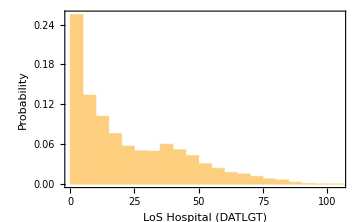

```mathematica
Histogram[DATLGT,Automatic,"Probability",Frame->True,FrameLabel->{"LoS Hospital (DATLGT)","Probability"},ImageSize->Medium]
```

### Files

```mathematica
data={{"ID","admissionH","HRecovery","HDeceased","HUCI","dischargeH","timeHOutcomeRDT","admissionUCI","UCIRecovery","UCIDeceased","UCIH","dischargeICU","timeICUOutcomeRDT"},Sequence@@Transpose[{casesHospUCIID,fHospAd//Values,fHospToCRd//Values,fHospToFd//Values,fHospTpUCId//Values,fHospDes//Values,If[Head[#]===Quantity,#,"Missing"]&/@(DATLGT//Values),fICUpAd//Values,fUCIToCRd//Values,fUCIToFd//Values,fUCIToHd//Values,DATDSI//Values,If[Head[#]===Quantity,#,"Missing"]&/@(DATLGTI//Values)}]};
```

```mathematica
data[[{1,2,3,4,-1}]]//Grid(*primera matrix -2020*)
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
7 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
12 | Sun 15 Mar 2020 | Wed 25 Mar 2020 |  |  | Wed 25 Mar 2020 | 10 days |  |  |  |  | Missing | Missing
848147 | Sat 3 Oct 2020 |  |  |  | Missing | Missing |  |  |  |  | Missing | Missing

```mathematica
Export["dataPrimeraM.m",data]
```

dataPrimeraM.m

```mathematica
masterM1=Import["/home/lina/Documents/datos_INS/masterM15-2020.m"];
```

```mathematica
masterM1[[1]]
```

{fecha,caso1,caso2,caso3,caso4,caso5,caso6,caso7,caso8,caso9,caso10,caso11,caso12,caso13,caso14,caso15,caso16,caso17,caso18,caso19,caso20,caso21,caso22,caso23,caso24,caso25,caso26,caso27,caso28,caso29,caso30,caso31,caso32,caso33,caso34,caso35,caso36,caso37,caso38,1048459,caso1048498,caso1048499,caso1048500,caso1048501,caso1048502,caso1048503,caso1048504,caso1048505,caso1048506,caso1048507,caso1048508,caso1048509,caso1048510,caso1048511,caso1048512,caso1048513,caso1048514,caso1048515,caso1048516,caso1048517,caso1048518,caso1048519,caso1048520,caso1048521,caso1048522,caso1048523,caso1048524,caso1048525,caso1048526,caso1048527,caso1048528,caso1048529,caso1048530,caso1048531,caso1048532,caso1048533,caso1048534,caso1048535,caso1048536}
 |  |  |  |

## Using the last matrices and groups

```mathematica
masterG=Import["/home/lina/Documents/datos_INS/masterG1.m"];
```

```mathematica
casesAdmitidosHosp=Import["/home/lina/Documents/datos_INS/casesAdmHospUCI_G1.m"];
```

```mathematica
casesHospUCIIDG=ToExpression/@casesAdmitidosHosp[[All,1]]; (* Este es el ID de los casos que entran al Hosp y/o ICU*)
```

```mathematica
masterM=Map[Transpose[{masterG[[All,1]],#}]&,casesAdmitidosHosp];(*Casos que entran al Hospital o UCI con fechas para las funcionesn*)
```

```mathematica
(*************************************************************************)
```

```mathematica
(*From G2 to G5 are there all the cases ?*)
```

```mathematica
masterG=Import["/home/lina/Documents/datos_INS/masterG2.m"];
```

```mathematica
masterG[[1]]
```

{fecha,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,1218377,1218459,1218460,1218461,1218462,1218463,1218464,1218465,1218466,1218467,1218468,1218469,1218470,1218471,1218472,1218473,1218474,1218475,1218476,1218477,1218478,1218479,1218480,1218481,1218482,1218483,1218484,1218485,1218486,1218487,1218488,1218489,1218490,1218491,1218492,1218493,1218494,1218495,1218496,1218497,1218498,1218499,1218500,1218501,1218502,1218503,1218504,1218505,1218506,1218507,1218508,1218509,1218510,1218511,1218512,1218513,1218514,1218515,1218516,1218517,1218518,1218519,1218520,1218521,1218522,1218523,1218524,1218525,1218526,1218527,1218528,1218529,1218530,1218531,1218532,1218533,1218534,1218535,1218536,1218537,1218538,1218539,1218540}
 |  |  |  |

```mathematica
masterG1=Import["/home/lina/Documents/datos_INS/masterG3.m"];
```

```mathematica
masterG1[[1]]
```

{fecha,1949668,1949669,1949670,1949671,1949672,1949673,1949674,1949675,1949676,1949677,1949678,1949679,1949680,1949681,1949682,1949683,1949684,1949685,1949686,1949687,1949688,1949689,1949690,1949691,1949692,1949693,1949694,1949695,1949696,1949697,1949698,1949699,1949700,1949701,1949702,1949703,1949704,1949705,1949706,1949707,1949708,1949709,1949710,1949711,1949712,1949713,1949714,1949715,1949716,1949717,1949718,1949719,1949720,1949721,1949722,974722,2924445,2924446,2924447,2924448,2924449,2924450,2924451,2924452,2924453,2924454,2924455,2924456,2924457,2924458,2924459,2924460,2924461,2924462,2924463,2924464,2924465,2924466,2924467,2924468,2924469,2924470,2924471,2924472,2924473,2924474,2924475,2924476,2924477,2924478,2924479,2924480,2924481,2924482,2924483,2924484,2924485,2924486,2924487,2924488,2924489,2924490,2924491,2924492,2924493,2924494,2924495,2924496,2924497,2924498,2924499,2924500}
 |  |  |  |

```mathematica
masterG2=Import["/home/lina/Documents/datos_INS/masterG4.m"];
```

```mathematica
masterG2[[1]]
```

{fecha,2924501,2924502,2924503,2924504,2924505,2924506,2924507,2924508,2924509,2924510,2924511,2924512,2924513,2924514,2924515,2924516,2924517,2924518,2924519,2924520,2924521,2924522,2924523,2924524,2924525,2924526,2924527,2924528,2924529,2924530,2924531,2924532,2924533,2924534,2924535,2924536,2924537,2924538,2924539,2924540,2924541,2924542,2924543,2924544,2924545,2924546,2924547,2924548,2924549,2924550,2924551,2924552,2924553,2924554,2924555,974722,3899278,3899279,3899280,3899281,3899282,3899283,3899284,3899285,3899286,3899287,3899288,3899289,3899290,3899291,3899292,3899293,3899294,3899295,3899296,3899297,3899298,3899299,3899300,3899301,3899302,3899303,3899304,3899305,3899306,3899307,3899308,3899309,3899310,3899311,3899312,3899313,3899314,3899315,3899316,3899317,3899318,3899319,3899320,3899321,3899322,3899323,3899324,3899325,3899326,3899327,3899328,3899329,3899330,3899331,3899332,3899333}
 |  |  |  |

```mathematica
masterG3=Import["/home/lina/Documents/datos_INS/masterG5.m"];
```

```mathematica
masterG3[[1]]
```

{fecha,3899334,3899335,3899336,3899337,3899338,3899339,3899340,3899341,3899342,3899343,3899344,3899345,3899346,3899347,3899348,3899349,3899350,3899351,3899352,3899353,3899354,3899355,3899356,3899357,3899358,3899359,3899360,3899361,3899362,3899363,3899364,3899365,3899366,3899367,3899368,3899369,3899370,3899371,3899372,3899373,3899374,3899375,3899376,3899377,3899378,3899379,3899380,3899381,3899382,3899383,3899384,3899385,3899386,3899387,3899388,974722,4874111,4874112,4874113,4874114,4874115,4874116,4874117,4874118,4874119,4874120,4874121,4874122,4874123,4874124,4874125,4874126,4874127,4874128,4874129,4874130,4874131,4874132,4874133,4874134,4874135,4874136,4874137,4874138,4874139,4874140,4874141,4874142,4874143,4874144,4874145,4874146,4874147,4874148,4874149,4874150,4874151,4874152,4874153,4874154,4874155,4874156,4874157,4874158,4874159,4874160,4874161,4874162,4874163,4874164,4874165,4874166}
 |  |  |  |

### Times in Hospital

```mathematica
fHospAd=(#[[1,2]]->adHospital[#])&/@masterM//Association;
```

```mathematica
fHospToCRd=(#[[1,2]]->fHospToCR[#])&/@masterM//Association;
```

```mathematica
fHospToFd=(#[[1,2]]->fHospToF[#])&/@masterM//Association;
```

```mathematica
fHospTpUCId=(#[[1,2]]->fHospToUCI[#])&/@masterM//Association;
```

```mathematica
cases=AssociationThread[masterM[[All,1,2]],"Missing"];
```

```mathematica
fHospDes=Join[cases,DeleteCases[fHospToCRd,""],DeleteCases[fHospToFd,""],DeleteCases[fHospTpUCId,""]];(*Discharge from Hospital*)
```

```mathematica
DATLGT=fHospDes-fHospAd(* Length of stay in hospital*);
```

### Times in ICU

```mathematica
fICUpAd=(#[[1,2]]->adUCI[#])&/@masterM//Association;
```

```mathematica
fUCIToCRd=(#[[1,2]]->fUCIToCR[#])&/@masterM//Association;
```

```mathematica
fUCIToFd=(#[[1,2]]->fUCIToF[#])&/@masterM//Association;
```

```mathematica
fUCIToHd=(#[[1,2]]->fUCIToH[#])&/@masterM//Association;
```

```mathematica
DATDSI=Join[cases,DeleteCases[fUCIToCRd,""],DeleteCases[fUCIToFd,""],DeleteCases[fUCIToHd,""]];(*Discharge from Hospital*)
```

```mathematica
DATLGTI=DATDSI-fICUpAd(* Length of stay in UCI*);
```

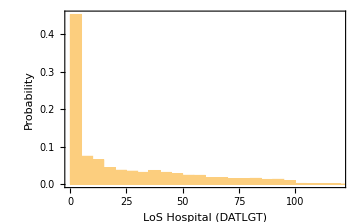

```mathematica
Histogram[DATLGT,Automatic,"Probability",Frame->True,FrameLabel->{"LoS Hospital (DATLGT)","Probability"},ImageSize->Medium]
```

### Files

```mathematica
data={{"ID","admissionH","HRecovery","HDeceased","HUCI","dischargeH","timeHOutcomeRDT","admissionUCI","UCIRecovery","UCIDeceased","UCIH","dischargeICU","timeICUOutcomeRDT"},Sequence@@Transpose[{casesHospUCIIDG,fHospAd//Values,fHospToCRd//Values,fHospToFd//Values,fHospTpUCId//Values,fHospDes//Values,If[Head[#]===Quantity,#,"Missing"]&/@(DATLGT//Values),fICUpAd//Values,fUCIToCRd//Values,fUCIToFd//Values,fUCIToHd//Values,DATDSI//Values,If[Head[#]===Quantity,#,"Missing"]&/@(DATLGTI//Values)}]};
```

```mathematica
data[[{1,2,3,4,-1}]]//Grid(*G1*)
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
7 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
12 | Sun 15 Mar 2020 | Wed 25 Mar 2020 |  |  | Wed 25 Mar 2020 | 10 days |  |  |  |  | Missing | Missing
974832 | Sat 14 Nov 2020 | Sun 15 Nov 2020 |  |  | Sun 15 Nov 2020 | 1 day |  |  |  |  | Missing | Missing

```mathematica
data[[{1,2,3,4,-1}]]//Grid(*G2*)
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
974837 |  |  |  |  | Missing | Missing | Sat 14 Nov 2020 | Sun 15 Nov 2020 |  |  | Sun 15 Nov 2020 | 1 day
974839 | Wed 21 Oct 2020 | Thu 12 Nov 2020 |  |  | Thu 12 Nov 2020 | 22 days |  |  |  |  | Missing | Missing
974842 | Wed 21 Oct 2020 | Thu 5 Nov 2020 |  |  | Thu 5 Nov 2020 | 15 days | Mon 9 Nov 2020 | Tue 10 Nov 2020 |  |  | Tue 10 Nov 2020 | 1 day
1949570 | Thu 18 Feb 2021 | Fri 26 Mar 2021 |  |  | Fri 26 Mar 2021 | 36 days |  |  |  |  | Missing | Missing

```mathematica
data[[{1,2,3,4,-1}]]//Grid(*G2a*)
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
7 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
12 | Sun 15 Mar 2020 | Wed 25 Mar 2020 |  |  | Wed 25 Mar 2020 | 10 days |  |  |  |  | Missing | Missing
609269 | Mon 31 Aug 2020 | Sun 11 Oct 2020 |  |  | Sun 11 Oct 2020 | 41 days |  |  |  |  | Missing | Missing

```mathematica
data[[{1,2,3,4,-1}]]//Grid(*G2b*)
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
609276 | Thu 12 Nov 2020 | Fri 13 Nov 2020 |  |  | Fri 13 Nov 2020 | 1 day |  |  |  |  | Missing | Missing
609279 | Sat 14 Nov 2020 | Sun 15 Nov 2020 |  |  | Sun 15 Nov 2020 | 1 day |  |  |  |  | Missing | Missing
609283 | Mon 31 Aug 2020 | Wed 30 Sep 2020 |  |  | Wed 30 Sep 2020 | 30 days |  |  |  |  | Missing | Missing
1218489 |  |  |  |  | Missing | Missing | Sun 29 Nov 2020 |  | Mon 30 Nov 2020 |  | Mon 30 Nov 2020 | 1 day

```mathematica
data[[{1,2,3,4,-1}]]//Grid(*G3*)
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
1949724 |  |  |  |  | Missing | Missing | Sun 14 Feb 2021 | Fri 14 May 2021 |  |  | Fri 14 May 2021 | 89 days
1949769 |  |  |  |  | Missing | Missing | Sun 24 Jan 2021 | Sun 31 Jan 2021 |  |  | Sun 31 Jan 2021 | 7 days
1949828 | Sat 30 Jan 2021 | Thu 4 Feb 2021 |  |  | Thu 4 Feb 2021 | 5 days |  |  |  |  | Missing | Missing
2924492 | Mon 31 May 2021 | Tue 1 Jun 2021 |  |  | Tue 1 Jun 2021 | 1 day |  |  |  |  | Missing | Missing

```mathematica
data[[{1,2,3,4,-1}]]//Grid(*G4*)
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
2924537 | Wed 5 May 2021 | Tue 20 Jul 2021 |  |  | Tue 20 Jul 2021 | 76 days |  |  |  |  | Missing | Missing
2924542 |  |  |  |  | Missing | Missing | Fri 7 May 2021 | Fri 21 May 2021 |  |  | Fri 21 May 2021 | 14 days
2924548 |  |  |  |  | Missing | Missing | Thu 6 May 2021 | Thu 13 May 2021 |  |  | Thu 13 May 2021 | 7 days
3899270 | Sat 19 Jun 2021 |  | Sun 20 Jun 2021 |  | Sun 20 Jun 2021 | 1 day |  |  |  |  | Missing | Missing

```mathematica
data[[1;;7]]//Grid(*G5*)
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
3899434 | Sat 19 Jun 2021 |  |  |  | Missing | Missing |  |  |  |  | Missing | Missing
3899435 | Sat 19 Jun 2021 |  |  |  | Missing | Missing |  |  |  |  | Missing | Missing
3899505 | Sat 19 Jun 2021 |  | Sun 20 Jun 2021 |  | Sun 20 Jun 2021 | 1 day |  |  |  |  | Missing | Missing
3899595 | Sat 19 Jun 2021 |  |  |  | Missing | Missing |  |  |  |  | Missing | Missing
3899637 | Sat 19 Jun 2021 |  |  |  | Missing | Missing |  |  |  |  | Missing | Missing
3899647 | Sat 19 Jun 2021 |  |  | Fri 23 Jul 2021 | Fri 23 Jul 2021 | 34 days | Fri 23 Jul 2021 |  |  | Thu 12 Aug 2021 | Thu 12 Aug 2021 | 20 days

```mathematica
Export["/home/lina/Documents/datos_INS/dataG1.m",data]
```

/home/lina/Documents/datos_INS/dataG1.m

```mathematica
Export["/home/lina/Documents/datos_INS/dataG2.m",data]
```

dataG2.m

```mathematica
Export["/home/lina/Documents/datos_INS/dataG2a.m",data]
```

dataG2a.m

```mathematica
Export["/home/lina/Documents/datos_INS/dataG2b.m",data]
```

dataG2b.m

```mathematica
Export["/home/lina/Documents/datos_INS/dataG3.m",data]
```

dataG3.m

```mathematica
Export["/home/lina/Documents/datos_INS/dataG4.m",data]
```

dataG4.m

```mathematica
Export["/home/lina/Documents/datos_INS/dataG5.m",data]
```

/home/lina/Documents/datos_INS/dataG5.m

## General Data Base

### Building the database

```mathematica
(**************************************************************)
```

```mathematica
m1=Import["/home/lina/Documents/datos_INS/masterM15-2020.m"];
```

```mathematica
m1[[2]]
```

{2020-03-15,casa,hospital,casa,casa,casa,casa,hospital,casa,casa,casa,casa,hospital,hospital,hospital,casa,casa,casa,casa,hospital,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,casa,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,1048308,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}
 |  |  |  |

```mathematica
m1[[1]]
```

{fecha,caso1,caso2,caso3,caso4,caso5,caso6,caso7,caso8,caso9,caso10,caso11,caso12,caso13,caso14,caso15,caso16,caso17,caso18,caso19,caso20,caso21,caso22,caso23,caso24,caso25,caso26,caso27,caso28,caso29,caso30,caso31,caso32,caso33,caso34,caso35,caso36,caso37,caso38,1048459,caso1048498,caso1048499,caso1048500,caso1048501,caso1048502,caso1048503,caso1048504,caso1048505,caso1048506,caso1048507,caso1048508,caso1048509,caso1048510,caso1048511,caso1048512,caso1048513,caso1048514,caso1048515,caso1048516,caso1048517,caso1048518,caso1048519,caso1048520,caso1048521,caso1048522,caso1048523,caso1048524,caso1048525,caso1048526,caso1048527,caso1048528,caso1048529,caso1048530,caso1048531,caso1048532,caso1048533,caso1048534,caso1048535,caso1048536}
 |  |  |  |

```mathematica
mG5=Import["/home/lina/Documents/datos_INS/masterG5.m"];
```

```mathematica
mG5[[-1]]
```

{2021-08-17,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Fallecido,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Fallecido,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,974708,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa,Casa}
 |  |  |  |

```mathematica
(****Nuesta base de datos incluye los casos desde 15 de marzo del 2020 hasta 17 de agosto del 2021***)
```

```mathematica
(************************************************************)
```

```mathematica
dataG5=Import["/home/lina/Documents/datos_INS/dataG5.m"];
```

$Aborted

```mathematica
dataG4=Import["/home/lina/Documents/datos_INS/dataG4.m"];
```

```mathematica
dataG3=Import["/home/lina/Documents/datos_INS/dataG3.m"];
```

```mathematica
dataG2=Import["/home/lina/Documents/datos_INS/dataG2.m"];
```

```mathematica
dataG1=Import["/home/lina/Documents/datos_INS/dataG1.m"];
```

```mathematica
dataGprimera=Import["/home/lina/Documents/datos_INS/dataPrimeraM.m"];
```

```mathematica
(*************************************************************)
```

```mathematica
dataGprimera[[All,1]]
```

{ID,2,7,12,13,14,16,19,33,57,64,68,69,81,86,95,108,133,152,153,157,163,168,176,184,185,187,188,200,202,207,208,216,227,232,233,234,235,236,240,246,250,257,260,261,266,269,273,274,278,282,286,290,303,309,332,335,341,351,361,371,372,374,385,386,387,394,395,412,415,418,421,434,460,468,478,481,492,499,502,510,511,514,65524,845854,845856,845857,845859,845863,845865,845872,845874,845881,845886,845889,845897,845912,845913,845936,845960,845971,845976,845988,845989,846008,846014,846018,846026,846047,846051,846052,846064,846070,846083,846088,846096,846102,846118,846133,846149,846156,846161,846170,846187,846245,846247,846265,846266,846277,846279,846293,846299,846301,846306,846323,846338,846344,846350,846356,846365,846369,846372,846391,846392,846393,846408,846445,846469,846472,846478,846482,846490,846495,846510,846532,846533,846567,846584,846589,846777,847074,847119,847167,847680,848126,848136,848147}
 |  |  |  |

```mathematica
dataG1c[[All,1]]//Short
```

{848148,848155,848274,848275,848320,848325,848334,848403,848410,848422,848437,848444,848446,848468,848481,848498,«12417»,974777,974779,974780,974784,974785,974787,974788,974793,974795,974806,974809,974810,974812,974814,974820,974832}

```mathematica
dataG1[[All,1]]
```

{ID,2,7,12,13,14,16,19,33,57,61,64,68,69,81,86,95,108,133,152,153,157,163,168,176,184,185,187,188,200,202,207,208,216,227,232,233,234,235,236,240,246,250,257,260,261,266,269,270,273,274,275,278,282,286,290,297,303,309,332,335,341,351,357,361,363,371,372,374,384,385,386,387,394,395,409,412,415,418,421,434,460,468,111079,974228,974229,974233,974237,974245,974255,974256,974264,974279,974287,974293,974312,974317,974343,974351,974366,974368,974380,974388,974390,974396,974398,974431,974432,974440,974447,974452,974455,974478,974510,974518,974526,974529,974536,974544,974572,974576,974580,974603,974605,974611,974613,974620,974628,974629,974630,974635,974638,974643,974648,974651,974656,974659,974660,974661,974681,974688,974689,974716,974721,974724,974729,974762,974765,974768,974770,974776,974777,974779,974780,974784,974785,974787,974788,974793,974795,974806,974809,974810,974812,974814,974820,974832}
 |  |  |  |

```mathematica
dataG2[[All,1]]
```

{ID,974837,974839,974842,974843,974845,974847,974851,974873,974897,974900,974905,974908,974925,974930,974944,974951,974953,974959,974963,974967,974971,975007,975016,975018,975024,975035,975037,975041,975045,975050,975053,975067,975075,975089,975093,975096,975104,975135,975184,975185,975190,975191,975192,975193,975200,975201,975210,975216,975223,975230,975231,975234,975242,975244,975249,975253,975257,975259,975261,63665,1948554,1948572,1948583,1948589,1948590,1948637,1948646,1948649,1948664,1948666,1948672,1948674,1948676,1948677,1948681,1948683,1948686,1948689,1948702,1948711,1948845,1949029,1949032,1949070,1949083,1949103,1949113,1949141,1949144,1949158,1949159,1949175,1949207,1949209,1949215,1949228,1949231,1949232,1949236,1949237,1949244,1949250,1949251,1949254,1949257,1949260,1949264,1949266,1949269,1949274,1949275,1949277,1949284,1949290,1949291,1949298,1949302,1949311,1949324,1949570}
 |  |  |  |

```mathematica
(* Al parcer hay casos que el dtaGprimera no se evaluaron porque no estaba la secuencia completa y que en dataG2 no se tuvieron en cuenta porque hacian parte de G1. ENTONCES HACER EL G1!!!!!!!!!!!!!!!!!!!!!!*)
```

```mathematica
dataG3[[All,1]]
```

{ID,1949724,1949769,1949828,1949936,1949994,1950025,1950063,1950140,1950169,1950217,1950239,1950282,1950285,1950289,1950290,1950291,1950294,1950329,1950337,1950366,1950397,1950403,1950412,1950413,1950415,1950422,1950428,1950430,1950432,1950436,1950453,1950467,1950482,1950505,1950508,1950514,1950526,1950527,1950534,1950537,1950538,1950539,1950547,1950549,1950550,1950556,1950559,1950568,1950571,1950573,1950575,1950576,1950577,1950578,1950580,42849,2923730,2923732,2923733,2923739,2923747,2923758,2923765,2923770,2923774,2923783,2923799,2923802,2923823,2923888,2923920,2923934,2923946,2923962,2923985,2924019,2924020,2924028,2924075,2924144,2924216,2924217,2924220,2924224,2924294,2924307,2924309,2924318,2924321,2924328,2924338,2924350,2924364,2924367,2924368,2924373,2924382,2924383,2924386,2924387,2924398,2924407,2924410,2924411,2924455,2924456,2924458,2924459,2924476,2924482,2924488,2924492}
 |  |  |  |

```mathematica
dataG4[[All,1]]
```

{ID,2924537,2924542,2924548,2924550,2924551,2924560,2924561,2924564,2924572,2924577,2924581,2924592,2924599,2924606,2924608,2924613,2924614,2924622,2924628,2924634,2924638,2924643,2924655,2924669,2924672,2924689,2924704,2924709,2924720,2924722,2924724,2924725,2924748,2924750,2924758,2924766,2924767,2924781,2924782,2924784,2924804,2924824,2924833,2924854,2924873,2924902,2924907,2924924,2924938,2924957,2924965,2924986,2925004,2925009,2925012,32072,3897776,3897785,3897787,3897788,3897789,3897791,3898141,3898142,3898176,3898190,3898194,3898195,3898199,3898331,3898479,3898532,3898553,3898565,3898568,3898579,3898593,3898661,3898670,3898686,3898821,3898832,3898872,3898878,3898883,3898885,3898889,3898917,3898921,3898922,3898953,3898955,3898968,3898973,3898984,3898993,3899003,3899012,3899019,3899063,3899088,3899122,3899128,3899138,3899173,3899184,3899185,3899192,3899212,3899213,3899256,3899270}
 |  |  |  |

```mathematica
dataG5[[All,1]]
```

{ID,3899434,3899435,3899505,3899595,3899637,3899647,3899736,3899739,3899950,3900083,3900159,3900318,3900322,3900324,3900348,3900381,3900661,3900808,3901243,3901418,3901523,3901616,3902020,3902467,3902589,3902637,3902642,3902647,3902801,3902826,3902881,3902977,3903007,3903019,3903077,3903119,3903137,3903166,3903172,3903258,3903288,3903346,3903419,3903502,3903544,3903665,3903690,3904041,3904097,3904101,3904103,3904117,3904239,3904243,3904309,21600,4868234,4868237,4868262,4868313,4868715,4868728,4869043,4869102,4869115,4869132,4869140,4869186,4869193,4869810,4870035,4870368,4870398,4870926,4870933,4870941,4870953,4870955,4870956,4870962,4870968,4871013,4871023,4871120,4871122,4871135,4871151,4871153,4871171,4871173,4871175,4871241,4871249,4871250,4871255,4871256,4871263,4871268,4871272,4871273,4871278,4871346,4871824,4871832,4872138,4872157,4872173,4872182,4872572,4872613,4873213,4873463}
 |  |  |  |

```mathematica
(*******************************************************+**Los casos que se solapan en dataGprimera y dataG1 son cohincidentes?***)
```

```mathematica
dataGprimera//Length
```

65690

```mathematica
dataGprimera[[{2,1000,3000,10000,20000,60000,8000}]]//Grid
```

2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
5034 | Mon 4 May 2020 | Tue 26 May 2020 |  |  | Tue 26 May 2020 | 22 days |  |  |  |  | Missing | Missing
16733 | Tue 19 May 2020 | Thu 21 May 2020 |  |  | Thu 21 May 2020 | 2 days |  |  |  |  | Missing | Missing
77107 | Wed 24 Jun 2020 | Thu 25 Jun 2020 |  |  | Thu 25 Jun 2020 | 1 day |  |  |  |  | Missing | Missing
175962 | Fri 17 Jul 2020 |  |  | Fri 7 Aug 2020 | Fri 7 Aug 2020 | 21 days | Fri 7 Aug 2020 | Mon 10 Aug 2020 |  |  | Mon 10 Aug 2020 | 3 days
751476 | Sat 19 Sep 2020 |  |  |  | Missing | Missing |  |  |  |  | Missing | Missing
58349 |  |  |  |  | Missing | Missing | Thu 18 Jun 2020 |  | Fri 3 Jul 2020 |  | Fri 3 Jul 2020 | 15 days

```mathematica
Table[Select[dataG1,#[[1]]==i&],{i,{2,5034,16733,77107,175962,751476,58349}}]//Flatten[#,1]&//Grid
```

2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
5034 | Mon 4 May 2020 | Tue 26 May 2020 |  |  | Tue 26 May 2020 | 22 days |  |  |  |  | Missing | Missing
16733 | Tue 19 May 2020 | Thu 21 May 2020 |  |  | Thu 21 May 2020 | 2 days |  |  |  |  | Missing | Missing
77107 | Wed 24 Jun 2020 | Thu 25 Jun 2020 |  |  | Thu 25 Jun 2020 | 1 day |  |  |  |  | Missing | Missing
175962 | Fri 17 Jul 2020 |  |  | Fri 7 Aug 2020 | Fri 7 Aug 2020 | 21 days | Fri 7 Aug 2020 | Mon 10 Aug 2020 |  |  | Mon 10 Aug 2020 | 3 days
751476 | Sat 19 Sep 2020 | Thu 12 Nov 2020 |  |  | Thu 12 Nov 2020 | 54 days |  |  |  |  | Missing | Missing
58349 |  |  |  |  | Missing | Missing | Thu 18 Jun 2020 |  | Fri 3 Jul 2020 |  | Fri 3 Jul 2020 | 15 days

```mathematica
dataGprimera[[-1]]
```

{848147,Sat 3 Oct 2020,,,,Missing,Missing,,,,,Missing,Missing}

```mathematica
Select[dataG1,#[[1]]==848147&]
```

{{848147,Sat 3 Oct 2020,Thu 12 Nov 2020,,,Thu 12 Nov 2020,40 days,,,,,Missing,Missing}}

```mathematica
Position[dataG1,{848147,__}]
```

{{98796}}

```mathematica
dataG1c=dataG1[[98796+1;;]];(*Este es el complemento, es lo que hay en dataG1 que no hay en dataGprimera*)
```

```mathematica
(*************************************************************)
```

```mathematica
dataINS=Import["/home/lina/Documents/datos_INS/2021-08-17.csv"];
```

```mathematica
dataINS[[1]]//PositionIndex
```

<|fecha_hoy_casos→{1},Caso→{2},Fecha Not→{3},Departamento→{4},Departamento_nom→{5},Ciudad_municipio→{6},Ciudad_municipio_nom→{7},Edad→{8},unidad_medida→{9},Sexo→{10},Fuente_tipo_contagio→{11},Ubicacion→{12},Estado→{13},Pais_viajo_1_cod→{14},Pais_viajo_1_nom→{15},Recuperado→{16},Fecha_inicio_sintomas→{17},Fecha_muerte→{18},Fecha_diagnostico→{19},Fecha_recuperado→{20},Tipo_recuperacion→{21},per_etn_→{22},nom_grupo_→{23}|>

```mathematica
dataINS[[2]]//PositionIndex
```

<|6/3/2020 0:00:00→{1,19},1→{2,9},2/3/2020 0:00:00→{3},11→{4},BOGOTA→{5,7},11001→{6},19→{8},F→{10},Importado→{11},Casa→{12},Leve→{13},380→{14},ITALIA→{15},Recuperado→{16},27/2/2020 0:00:00→{17},→{18,23},13/3/2020 0:00:00→{20},PCR→{21},6→{22}|>

```mathematica
(dataINS//Length)-1 (* Number of cases *)
```

4874169

```mathematica
(dataG2[[1]]//Length)-1 (* Number of new columnas, se quita la primera porque es el ID-position *)
```

12

```mathematica
templateNewColumns=Table[{"","","","","","","","","","","",""},(dataINS//Length)-1 ];
```

```mathematica
dataHospUCItotal=Join[(*dataGprimera,*)dataG1,dataG2[[2;;]],dataG3[[2;;]],dataG4[[2;;]],dataG5[[2;;]]];(*No se va usar dataGprimera porque segun la Revision es mejor la info en G1*)
```

```mathematica
dataHospUCItotal[[{1,2,-1}]]//Grid
```

ID | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
4873463 |  |  |  |  | Missing | Missing | Tue 17 Aug 2021 |  |  |  | Missing | Missing

```mathematica
Length[dataHospUCItotal]
```

271883

```mathematica
Total[Length/@{dataGprimera,dataG2,dataG3,dataG4,dataG5}]
```

226332

```mathematica
MapThread[(templateNewColumns[[#1]]=#2)&,{dataHospUCItotal[[2;;,1]],dataHospUCItotal[[2;;,2;;]]}];
```

```mathematica
templateNewColumns[[1;;5]]//Grid
```

|  |  |  |  |  |  |  |  |  |  | 
Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
 |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |

```mathematica
dataINSNew={{dataINS[[1,{2,5,7,8,9,10,22,12,13,16,17,18,19,20}]],dataG1[[1,2;;]]}//Flatten,Sequence@@Map[Flatten,Transpose[{dataINS[[2;;,{2,5,7,8,9,10,22,12,13,16,17,18,19,20}]],templateNewColumns}]]};
```

```mathematica
Export["/home/lina/Documents/datos_INS/dataINSNew.csv",dataINSNew,"CSV"]
```

/home/lina/Documents/datos_INS/dataINSNew.csv

```mathematica
dataINSNew[[1;;2]]
```

{{Caso,Departamento_nom,Ciudad_municipio_nom,Edad,unidad_medida,Sexo,per_etn_,Ubicacion,Estado,Recuperado,Fecha_inicio_sintomas,Fecha_muerte,Fecha_diagnostico,Fecha_recuperado,admissionH,HRecovery,HDeceased,HUCI,dischargeH,timeHOutcomeRDT,admissionUCI,UCIRecovery,UCIDeceased,UCIH,dischargeICU,timeICUOutcomeRDT},{1,BOGOTA,BOGOTA,19,1,F,6,Casa,Leve,Recuperado,27/2/2020 0:00:00,,6/3/2020 0:00:00,13/3/2020 0:00:00,,,,,,,,,,,,}}

```mathematica
Length/@%26
```

{36,26}

### Reviewing the database

```mathematica
dataINSNew=Import["/home/lina/Documents/datos_INS/dataINSNew.csv"];
```

```mathematica
dataINSNew[[1]]//PositionIndex
```

<|Caso→{1},Departamento_nom→{2},Ciudad_municipio_nom→{3},Edad→{4},unidad_medida→{5},Sexo→{6},per_etn_→{7},Ubicacion→{8},Estado→{9},Recuperado→{10},Fecha_inicio_sintomas→{11},Fecha_muerte→{12},Fecha_diagnostico→{13},Fecha_recuperado→{14},admissionH→{15},HRecovery→{16},HDeceased→{17},HUCI→{18},dischargeH→{19},timeHOutcomeRDT→{20},admissionUCI→{21},UCIRecovery→{22},UCIDeceased→{23},UCIH→{24},dischargeICU→{25},timeICUOutcomeRDT→{26}|>

```mathematica
(*********************************************************************************Gprimera y G1*)
```

```mathematica
dataGprimera[[{2,20000,-1}]]//Grid
```

2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  | Mon 23 Mar 2020 | 8 days |  |  |  |  | Missing | Missing
175962 | Fri 17 Jul 2020 |  |  | Fri 7 Aug 2020 | Fri 7 Aug 2020 | 21 days | Fri 7 Aug 2020 | Mon 10 Aug 2020 |  |  | Mon 10 Aug 2020 | 3 days
848147 | Sat 3 Oct 2020 |  |  |  | Missing | Missing |  |  |  |  | Missing | Missing

```mathematica
(***caso1)
```

```mathematica
dataINSNew[[2+1]]//PositionIndex
```

<|2→{1},VALLE→{2},BUGA→{3},34→{4},1→{5},M→{6},5→{7},Casa→{8},Leve→{9},Recuperado→{10},4/3/2020 0:00:00→{11},→{12,17,18,21,22,23,24},9/3/2020 0:00:00→{13},19/3/2020 0:00:00→{14},Sun 15 Mar 2020→{15},Mon 23 Mar 2020→{16,19},8 days→{20},Missing→{25,26}|>

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2020-03-15.xlsx"];
```

```mathematica
caso[[1,2+1]]
```

{2.,Mon 9 Mar 2020 00:00:00GMT-5,Buga,Hospital,,,,X,,,,,,,,X,X,,}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2020-03-23.xlsx"];
```

```mathematica
caso[[1,2+1]]
```

{2.,Mon 9 Mar 2020 00:00:00GMT-5,Buga,Valle,recuperado,30 a 39,M,Importado,España}

```mathematica
(***caso2)
```

```mathematica
dataINSNew[[848147+1]]//PositionIndex
```

<|848187→{1},BOGOTA→{2,3},55→{4},1→{5},M→{6},6→{7},Casa→{8},Leve→{9},Recuperado→{10},13/9/2020 0:00:00→{11},→{12,16,17,18,21,22,23,24},18/9/2020 0:00:00→{13},30/10/2020 0:00:00→{14},Sat 3 Oct 2020→{15},Missing→{19,20,25,26}|>

```mathematica
Select[dataG1,#[[1]]==848147&]
```

{{848147,Sat 3 Oct 2020,Thu 12 Nov 2020,,,Thu 12 Nov 2020,40 days,,,,,Missing,Missing}}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2020-10-03.xlsx"];
```

```mathematica
caso[[1,848147+1]]
```

{848187.,Wed 16 Sep 2020 00:00:00GMT-5,11,Bogotá D.C.,11001,Bogotá D.C.,55.,M,En estudio,Hospital,Moderado,170,COLOMBIA,,,Sun 13 Sep 2020 00:00:00GMT-5,,Fri 18 Sep 2020 00:00:00GMT-5,,Sat 3 Oct 2020 00:00:00GMT-5,Hospital,,,}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2020-10-30.csv"];
```

```mathematica
caso1[[848147+1]]
```

{3/10/2020 0:00:00;848187;16/9/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";55;"1";"M";"En estudio";"Hospital";"Moderado";;;"Recuperado";13/9/2020 0:00:00;;18/9/2020 0:00:00;30/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2020-11-11.csv"];
```

```mathematica
caso3[[848147+1]]
```

{3/10/2020 0:00:00;848187;16/9/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";55;"1";"M";"En estudio";"Hospital";"Moderado";;;"Recuperado";13/9/2020 0:00:00;;18/9/2020 0:00:00;30/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2020-11-12.csv"];
```

```mathematica
caso2[[848147+1]]
```

{3/10/2020 0:00:00;848179;28/9/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";51;"1";"F";"En estudio";"Casa";"Leve";;;"Recuperado";18/9/2020 0:00:00;;30/9/2020 0:00:00;12/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
(* Esta mejor la info de dataG1 que de la primera matriz y la fecha de recuperacion del INS y la estimada pueden diferir porque se puede reportar como Recuṕerado aún cuando esta en el Hospital *)
```

```mathematica
(***caso3)
```

```mathematica
dataINSNew[[175962+1]]//PositionIndex
```

<|176002→{1},CUNDINAMARCA→{2},SOACHA→{3},64→{4},1→{5},M→{6},6→{7},Casa→{8},Leve→{9},Recuperado→{10},1/7/2020 0:00:00→{11},→{12,16,17,23,24},16/7/2020 0:00:00→{13},10/8/2020 0:00:00→{14},Fri 17 Jul 2020→{15},Fri 7 Aug 2020→{18,19,21},21 days→{20},Mon 10 Aug 2020→{22,25},3 days→{26}|>

```mathematica
Select[dataG1,#[[1]]==175962&]
```

{{175962,Fri 17 Jul 2020,,,Fri 7 Aug 2020,Fri 7 Aug 2020,21 days,Fri 7 Aug 2020,Mon 10 Aug 2020,,,Mon 10 Aug 2020,3 days}}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2020-10-03.xlsx"];
```

```mathematica
caso[[1,848147+1]]
```

```mathematica
(***caso4)
```

```mathematica
dataINSNew[[751476+1]]//PositionIndex
```

<|751516→{1},CESAR→{2},ROBLES (LA PAZ)→{3},74→{4},1→{5},M→{6},6→{7},Casa→{8},Leve→{9},Recuperado→{10},28/8/2020 0:00:00→{11},→{12,16,17,18,21,22,23,24},18/9/2020 0:00:00→{13},17/1/2021 0:00:00→{14},Sat 19 Sep 2020→{15},Missing→{19,20,25,26}|>

```mathematica
Select[dataG1,#[[1]]==751476&]
```

{{751476,Sat 19 Sep 2020,Thu 12 Nov 2020,,,Thu 12 Nov 2020,54 days,,,,,Missing,Missing}}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2020-11-12.csv"];
```

```mathematica
caso[[751476+1]]
```

{19/9/2020 0:00:00;751508;12/9/2020 0:00:00;"68";"SANTANDER";"68001";"BUCARAMANGA";60;"1";"M";"En estudio";"Casa";"Leve";;;"Recuperado";2/9/2020 0:00:00;;18/9/2020 0:00:00;25/9/2020 0:00:00;"Tiempo";"6";}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2020-11-11.csv"];
```

```mathematica
caso[[751476+1]]
```

{19/9/2020 0:00:00;751516;12/9/2020 0:00:00;"20";"CESAR";"20621";"ROBLES (LA PAZ)";74;"1";"M";"En estudio";"Hospital";"Moderado";;;"Activo";28/8/2020 0:00:00;;18/9/2020 0:00:00;;;"6";}

```mathematica
(*Creo que es mejor usar G1 que Gprimera porque es mas consecuente con lo que hay entre bases de datos.*)
```

```mathematica
(*********************************************************************************G2*)
```

```mathematica
dataG2[[{2,40000,-1}]]//Grid
```

974837 |  |  |  |  | Missing | Missing | Sat 14 Nov 2020 | Sun 15 Nov 2020 |  |  | Sun 15 Nov 2020 | 1 day
1443357 |  |  |  |  | Missing | Missing | Tue 15 Dec 2020 |  | Sat 2 Jan 2021 |  | Sat 2 Jan 2021 | 18 days
1949570 | Thu 18 Feb 2021 | Fri 26 Mar 2021 |  |  | Fri 26 Mar 2021 | 36 days |  |  |  |  | Missing | Missing

```mathematica
(***caso1)
```

```mathematica
dataINSNew[[974837+1]]//PositionIndex
```

<|974877→{1},HUILA→{2},PITALITO→{3},18→{4},1→{5},F→{6},6→{7},Casa→{8},Leve→{9},Recuperado→{10},8/10/2020 0:00:00→{11},→{12,15,16,17,18,23,24},19/10/2020 0:00:00→{13},10/4/2021 0:00:00→{14},Missing→{19,20},Sat 14 Nov 2020→{21},Sun 15 Nov 2020→{22,25},1 day→{26}|>

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2020-11-14.csv"];
```

```mathematica
caso[[974837+1]]
```

{13/8/2020 0:00:00;433188;9/8/2020 0:00:00;"11";"BOGOTA";"11001";"BOGOTA";58;"1";"F";"En estudio";"Hospital UCI";"Grave";;;"Activo";1/8/2020 0:00:00;;13/8/2020 0:00:00;;;"6";}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2020-11-15.csv"];
```

```mathematica
caso1[[974837+1]]
```

{21/10/2020 0:00:00;974877;16/10/2020 0:00:00;"41";"HUILA";"41551";"PITALITO";18;"1";"F";"Relacionado";"Casa";"Leve";;;"Recuperado";8/10/2020 0:00:00;;19/10/2020 0:00:00;23/10/2020 0:00:00;"Tiempo";"6";}

```mathematica
(***caso2)
```

```mathematica
dataINSNew[[1443357+1]]//PositionIndex
```

<|1443397→{1},VALLE→{2},CALI→{3},71→{4},1→{5},F→{6},6→{7},Fallecido→{8,9,10},5/12/2020 0:00:00→{11},1/1/2021 0:00:00→{12},14/12/2020 0:00:00→{13},→{14,15,16,17,18,22,24},Missing→{19,20},Tue 15 Dec 2020→{21},Sat 2 Jan 2021→{23,25},18 days→{26}|>

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2020-12-15.csv"];
```

```mathematica
caso[[1443357+1]]
```

{15/12/2020 0:00:00;1443397;13/12/2020 0:00:00;"76";"VALLE";"76001";"CALI";71;"1";"F";"En estudio";"Hospital UCI";"Grave";;;"Activo";5/12/2020 0:00:00;;14/12/2020 0:00:00;;;;}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-01-02.csv"];
```

```mathematica
caso1[[1443357+1]]
```

{15/12/2020 0:00:00,1443397,13/12/2020 0:00:00,76,VALLE,76001,CALI,71,1,F,En estudio,Fallecido,Fallecido,,,Fallecido,5/12/2020 0:00:00,1/1/2021 0:00:00,14/12/2020 0:00:00,,,6,}

```mathematica
(***caso3)
```

```mathematica
dataINSNew[[1949570+1]]//PositionIndex
```

<|1949610→{1},BOGOTA→{2,3},24→{4},1→{5},M→{6},6→{7},Casa→{8},Leve→{9},Recuperado→{10},7/1/2021 0:00:00→{11},→{12,17,18,21,22,23,24},18/1/2021 0:00:00→{13},1/2/2021 0:00:00→{14},Thu 18 Feb 2021→{15},Fri 26 Mar 2021→{16,19},36 days→{20},Missing→{25,26}|>

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-02-18.csv"];
```

```mathematica
caso[[1949570+1]]
```

{20/1/2021 0:00:00,1949610,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,24,1,M,En estudio,Hospital,Moderado,,,Recuperado,7/1/2021 0:00:00,,18/1/2021 0:00:00,1/2/2021 0:00:00,Tiempo,6,}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-03-25.csv"];
```

```mathematica
caso1[[1949570+1]]
```

{20/1/2021 0:00:00,1949610,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,24,1,M,En estudio,Hospital,Moderado,,,Recuperado,7/1/2021 0:00:00,,18/1/2021 0:00:00,1/2/2021 0:00:00,Tiempo,6,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-03-26.csv"];
```

```mathematica
caso2[[1949570+1]]
```

{20/1/2021 0:00:00,1949610,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,24,1,M,En estudio,Casa,Leve,,,Recuperado,7/1/2021 0:00:00,,18/1/2021 0:00:00,1/2/2021 0:00:00,Tiempo,6,}

```mathematica
(*dataG2 esta muy bien!!. Los errores que se presentan son debido a errores en la construccion de la data desde el INS:1. se translocan los casos, 2. se ponen fechas de recuperación a la vez que se situa al paciente en Hospital o ICU*)
```

```mathematica
(*********************************************************************************G3*)
```

```mathematica
dataG3[[{2,40000,-1}]]//Grid
```

1949724 |  |  |  |  | Missing | Missing | Sun 14 Feb 2021 | Fri 14 May 2021 |  |  | Fri 14 May 2021 | 89 days
2845712 | Fri 30 Apr 2021 | Fri 6 Aug 2021 |  |  | Fri 6 Aug 2021 | 98 days |  |  |  |  | Missing | Missing
2924492 | Mon 31 May 2021 | Tue 1 Jun 2021 |  |  | Tue 1 Jun 2021 | 1 day |  |  |  |  | Missing | Missing

```mathematica
(***caso1)
```

```mathematica
dataINSNew[[1949724+1]]//PositionIndex
```

<|1949764→{1},BOGOTA→{2,3},29→{4},1→{5},M→{6},6→{7},Fallecido→{8,9,10},18/1/2021 0:00:00→{11,13},27/6/2021 0:00:00→{12},→{14,15,16,17,18,23,24},Missing→{19,20},Sun 14 Feb 2021→{21},Fri 14 May 2021→{22,25},89 days→{26}|>

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-02-14.csv"];
```

```mathematica
caso[[1949724+1]]
```

{20/1/2021 0:00:00,1949764,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,29,1,M,En estudio,Hospital UCI,Grave,,,Recuperado,18/1/2021 0:00:00,,18/1/2021 0:00:00,1/2/2021 0:00:00,Tiempo,6,}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-05-13.csv"];
```

```mathematica
caso1[[1949724+1]]
```

{20/1/2021 0:00:00,1949764,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,29,1,M,En estudio,Hospital UCI,Grave,,,Recuperado,18/1/2021 0:00:00,,18/1/2021 0:00:00,1/2/2021 0:00:00,Tiempo,6,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-05-14.csv"];
```

```mathematica
caso2[[1949724+1]]
```

{20/1/2021 0:00:00,1949764,18/1/2021 0:00:00,11,BOGOTA,11001,BOGOTA,29,1,M,En estudio,Casa,Leve,,,Recuperado,18/1/2021 0:00:00,,18/1/2021 0:00:00,1/2/2021 0:00:00,Tiempo,6,}

```mathematica
(*********************************************************************************G4*)
```

```mathematica
dataG4[[{2,20000,-1}]]//Grid
```

2924537 | Wed 5 May 2021 | Tue 20 Jul 2021 |  |  | Tue 20 Jul 2021 | 76 days |  |  |  |  | Missing | Missing
3439855 | Wed 2 Jun 2021 | Sat 5 Jun 2021 |  |  | Sat 5 Jun 2021 | 3 days |  |  |  |  | Missing | Missing
3899270 | Sat 19 Jun 2021 |  | Sun 20 Jun 2021 |  | Sun 20 Jun 2021 | 1 day |  |  |  |  | Missing | Missing

```mathematica
(***caso1)
```

```mathematica
dataINSNew[[3439855+1]]//PositionIndex
```

<|3439895→{1},CUNDINAMARCA→{2},SOACHA→{3},26→{4},1→{5},F→{6},6→{7},Casa→{8},Leve→{9},Recuperado→{10},28/5/2021 0:00:00→{11},→{12,17,18,21,22,23,24},30/5/2021 0:00:00→{13},11/6/2021 0:00:00→{14},Wed 2 Jun 2021→{15},Sat 5 Jun 2021→{16,19},3 days→{20},Missing→{25,26}|>

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-06-02.csv"];
```

```mathematica
caso[[3439855+1]]
```

{2/6/2021 0:00:00,3439896,30/5/2021 0:00:00,66,RISARALDA,66170,DOSQUEBRADAS,83,1,M,En estudio,Hospital,Moderado,,,Activo,27/5/2021 0:00:00,,30/5/2021 0:00:00,,,,}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-06-05.csv"];
```

```mathematica
caso[[3439855+1]]
```

{2/6/2021 0:00:00,3439895,30/5/2021 0:00:00,25,CUNDINAMARCA,25754,SOACHA,26,1,F,En estudio,Casa,Leve,,,Activo,28/5/2021 0:00:00,,30/5/2021 0:00:00,,,6,}

```mathematica
(*********************************************************************************G5*)
```

```mathematica
dataG5[[{2,10000,-1}]]//Grid
```

3899434 | Sat 19 Jun 2021 |  |  |  | Missing | Missing |  |  |  |  | Missing | Missing
4387078 | Fri 9 Jul 2021 | Fri 16 Jul 2021 |  |  | Fri 16 Jul 2021 | 7 days |  |  |  |  | Missing | Missing
4873463 |  |  |  |  | Missing | Missing | Tue 17 Aug 2021 |  |  |  | Missing | Missing

```mathematica
(***caso1)
```

```mathematica
dataINSNew[[4387078+1]]//PositionIndex
```

<|4387118→{1},BOGOTA→{2,3},52→{4},1→{5},F→{6},6→{7},Casa→{8},Leve→{9},Recuperado→{10},28/6/2021 0:00:00→{11},→{12,17,18,21,22,23,24},5/7/2021 0:00:00→{13},17/7/2021 0:00:00→{14},Fri 9 Jul 2021→{15},Fri 16 Jul 2021→{16,19},7 days→{20},Missing→{25,26}|>

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-07-08.csv"];
```

```mathematica
caso[[4387078+1]]
```

{6/7/2021 0:00:00,4387118,30/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,52,1,F,En estudio,Casa,Leve,,,Activo,28/6/2021 0:00:00,,5/7/2021 0:00:00,,,,}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-07-09.csv"];
```

```mathematica
caso[[4387078+1]]
```

## Juan Data Base

```mathematica
dataINSNew=Import["/home/lina/Documents/UnCover/datos_INS/dataINSNew.csv"];
```

```mathematica
dataINSNew[[1]]//PositionIndex
```

<|Caso→{1},Departamento_nom→{2},Ciudad_municipio_nom→{3},Edad→{4},unidad_medida→{5},Sexo→{6},per_etn_→{7},Ubicacion→{8},Estado→{9},Recuperado→{10},Fecha_inicio_sintomas→{11},Fecha_muerte→{12},Fecha_diagnostico→{13},Fecha_recuperado→{14},admissionH→{15},HRecovery→{16},HDeceased→{17},HUCI→{18},dischargeH→{19},timeHOutcomeRDT→{20},admissionUCI→{21},UCIRecovery→{22},UCIDeceased→{23},UCIH→{24},dischargeICU→{25},timeICUOutcomeRDT→{26}|>

### variable 1:IPM

```mathematica
(*1. ID caso.2. Departamento (por código o nombre).3. Índice de pobreza multidimensional general por departamento.4. Índice barreras de acceso a servicios de salud por departamento.5. Índice hacinamiento crítico por departamento.6. Índice sin acceso a fuente de agua mejorada por departamento.7. Índice sin aseguramiento en salud por departamento.8. índice inadecuada eliminación de excretas por departamento.9. Índice bajo logro educativo.10. Municipio (por código o nombre*)
```

```mathematica
ipm=Import["/home/lina/Documents/datos_INS/Datos IPM.xlsx"];
```

```mathematica
ipm//Dimensions
```

{3}

```mathematica
ipm//Length
```

3

```mathematica
ipm[[1,1;;3]]
```

{{Departamento,IPM2019,BLE2019,BASS2019,HA2019,IEE2019,SAAM2019,SAS2019},{ANTIOQUIA,15.7,42.5,2.6,6.8,8.4,9.5,11.2},{ATLANTICO,14.9,31.6,6.7,13.9,10.4,3.3,13.3}}

```mathematica
ipm[[2,1;;3]]
```

{{Departamento,IPM2020,BLE2020,BASS2020,HA2020,IEE2020,SAAM2020,SAS2020,,,},{ANTIOQUIA,14.9,44.2,0.4,6.2,9.3,6.4,8.7,,,},{ATLANTICO,14.1,28.,1.1,13.8,6.7,2.9,10.,,,}}

```mathematica
ipm[[2]]//DeleteDuplicates
```

{{Departamento,IPM2020,BLE2020,BASS2020,HA2020,IEE2020,SAAM2020,SAS2020,,,},{ANTIOQUIA,14.9,44.2,0.4,6.2,9.3,6.4,8.7,,,},{ATLANTICO,14.1,28.,1.1,13.8,6.7,2.9,10.,,,},{BOGOTA,7.5,23.3,2.9,6.4,0.5,0.6,16.9,,,},{BOLIVAR,28.1,46.7,0.8,12.9,36.6,17.4,9.1,,,},{BOYACA,11.7,52.1,0.3,3.4,5.6,7.5,6.5,,,},{CALDAS,14.5,47.2,4.1,3.7,7.,8.7,10.6,,,},{CAQUETA,26.1,57.8,4.5,8.6,12.5,18.1,6.8,,,},{CAUCA,28.2,62.2,3.5,4.7,8.9,19.7,8.2,,,},{CESAR,27.2,46.1,0.6,17.,15.3,8.1,11.8,,,},{CORDOBA,31.8,53.9,0.7,10.9,18.5,19.,3.8,,,},{CUNDINAMARCA,11.4,40.8,0.7,4.7,3.4,6.4,12.5,,,},{CHOCO,49.,59.2,1.3,7.7,66.7,74.7,5.4,,,},{HUILA,23.4,53.6,6.4,6.2,6.4,11.5,7.4,,,},{GUAJIRA,51.7,59.4,2.4,24.9,49.4,48.,15.7,,,},{MAGDALENA,33.4,51.9,1.9,19.,29.2,17.2,9.5,,,},{META,14.1,42.4,2.8,5.1,5.3,13.3,8.,,,},{NARIÑO,27.3,61.8,6.3,7.7,18.5,22.7,7.1,,,},{NORTE SANTANDER,26.1,50.8,7.6,14.3,9.,12.3,17.5,,,},{QUINDIO,12.9,42.,2.2,4.3,2.1,3.,12.6,,,},{RISARALDA,13.1,42.7,0.9,3.8,4.8,6.8,9.4,,,},{SANTANDER,12.5,43.5,1.3,5.1,6.,9.8,7.8,,,},{SUCRE,38.1,57.5,3.6,14.9,28.8,10.7,7.2,,,},{TOLIMA,19.,51.6,6.4,6.2,5.8,9.7,10.,,,},{VALLE,11.1,34.9,1.2,4.4,3.,3.2,10.1,,,},{ARAUCA,26.1,54.8,2.4,9.7,11.1,5.2,18.,,,},{CASANARE,19.6,50.,2.3,10.,8.1,10.4,12.6,,,},{PUTUMAYO,27.8,58.9,3.4,5.9,8.4,37.2,7.4,,,},{SAN ANDRES,11.9,24.,0.,9.8,80.1,57.1,4.1,,,},{AMAZONAS,39.,48.2,0.4,14.2,34.,53.3,5.6,,,},{GUAINIA,65.9,61.9,3.2,16.6,64.5,77.2,10.7,,,},{GUAVIARE,34.6,56.1,6.8,9.7,25.3,46.,11.3,,,},{VAUPES,65.6,60.7,2.2,31.1,57.5,69.3,3.9,,,},{VICHADA,75.6,74.9,0.8,21.9,84.3,67.2,12.9,,,},{BARRANQUILLA,17.4,29.,3.,13.5,2.1,1.,20.1,,,},{CARTAGENA,19.9,33.5,2.5,14.2,7.8,5.4,17.6,,,},{STA MARTA D.E.,24.4,34.2,3.7,19.4,13.9,18.4,16.5,,,},{,,,,,,,,,,}}

```mathematica
ipm[[3,1;;3]]
```

{{Variable ,Codificación },{Departamento,Departamento },{IPM,Indice de pobreza multidimensional }}

```mathematica
imp2019rules=Thread[ipm[[1,2;;,1]]->ipm[[1,2;;,2;;]]]
```

{ANTIOQUIA→{15.7,42.5,2.6,6.8,8.4,9.5,11.2},ATLANTICO→{14.9,31.6,6.7,13.9,10.4,3.3,13.3},BOGOTA→{7.1,21.9,10.3,6.5,0.,0.1,13.5},BOLIVAR→{26.9,49.,4.,16.4,38.9,17.1,10.1},BOYACA→{12.8,55.,1.5,4.3,8.4,16.7,7.3},CALDAS→{14.3,51.1,4.7,4.3,5.3,12.1,9.2},CAQUETA→{25.7,62.9,4.3,8.7,14.3,24.,8.6},CAUCA→{24.,62.3,6.9,4.5,9.6,21.7,7.9},CESAR→{25.5,49.6,3.8,19.6,14.6,9.2,14.9},CORDOBA→{34.7,57.3,12.8,14.,23.8,26.5,6.9},CUNDINAMARCA→{12.3,44.6,2.9,6.5,5.6,10.4,12.8},CHOCO→{42.3,63.4,3.2,9.3,67.5,67.5,7.5},HUILA→{18.3,56.4,5.,6.1,7.4,14.4,7.3},GUAJIRA→{48.8,60.9,4.7,23.7,46.,42.9,25.6},MAGDALENA→{31.6,51.3,3.4,21.3,33.9,19.7,14.1},META→{19.1,48.4,9.5,6.7,5.,10.8,10.8},NARIÑO→{23.3,67.6,8.,7.9,16.9,23.,6.3},NORTE SANTANDER→{24.2,48.8,6.4,13.7,9.,13.5,17.5},QUINDIO→{10.2,42.,5.4,4.3,1.1,2.9,12.2},RISARALDA→{11.1,47.7,3.9,3.4,5.8,4.8,8.4},SANTANDER→{12.4,46.2,3.8,7.7,7.6,15.7,10.8},SUCRE→{33.3,58.7,7.4,14.1,25.9,12.5,9.7},TOLIMA→{15.2,50.5,5.2,5.5,8.8,14.2,7.3},VALLE→{10.8,42.3,2.4,4.6,6.,4.9,9.9},ARAUCA→{23.3,59.,0.9,9.8,10.4,6.8,20.},CASANARE→{18.3,53.7,3.6,9.7,6.9,8.4,11.1},PUTUMAYO→{25.4,62.9,5.7,9.3,13.,47.4,8.5},SAN ANDRES→{8.2,28.8,2.7,11.3,80.8,69.7,3.2},AMAZONAS→{35.6,49.4,0.9,15.4,44.3,64.,6.},GUAINIA→{67.,67.9,4.2,21.4,63.1,76.,10.5},GUAVIARE→{30.9,63.6,5.9,8.2,29.2,49.5,13.6},VAUPES→{66.5,71.2,1.8,35.6,72.6,77.,1.9},VICHADA→{72.2,75.,4.8,30.4,81.3,61.1,16.},BARRANQUILLA→{17.4,29.,3.,13.5,2.1,1.,20.1},CARTAGENA→{19.9,33.5,2.5,14.2,7.8,5.4,17.6},STA MARTA D.E.→{24.4,34.2,3.7,19.4,13.9,18.4,16.5}}

```mathematica
dataINSNew[[2;;,2]]//DeleteDuplicates
```

{BOGOTA,VALLE,ANTIOQUIA,CARTAGENA,HUILA,META,RISARALDA,NORTE SANTANDER,CALDAS,CUNDINAMARCA,BARRANQUILLA,SANTANDER,QUINDIO,TOLIMA,CAUCA,STA MARTA D.E.,CESAR,SAN ANDRES,CASANARE,NARIÑO,ATLANTICO,BOYACA,CORDOBA,BOLIVAR,SUCRE,MAGDALENA,GUAJIRA,CHOCO,AMAZONAS,CAQUETA,PUTUMAYO,ARAUCA,VAUPES,GUAINIA,VICHADA,GUAVIARE,Tolima,Caldas,GUAINIA }

```mathematica
Complement[ipm[[1,2;;,1]],%9]
```

{}

```mathematica
Complement[%9,ipm[[1,2;;,1]]]
```

```mathematica
{"Caldas","GUAINIA ","Tolima"}
```

```mathematica
imp2019={{"IPM_DEP_2019","BLE_DEP_2019","BASS_DEP_2019","HC_DEP_2019","IEE_DEP_2019","SAFAM_DEP_2019","SAS_DEP_2019"},Sequence@@(dataINSNew[[2;;,2]]/.{"Caldas"->"CALDAS","GUAINIA "->"GUAINIA","Tolima"->"TOLIMA"}/. imp2019rules)};
```

```mathematica
imp2019//DeleteDuplicates
```

{{IPM2019,BLE2019,BASS2019,HA2019,IEE2019,SAAM2019,SAS2019},{7.1,21.9,10.3,6.5,0.,0.1,13.5},{10.8,42.3,2.4,4.6,6.,4.9,9.9},{15.7,42.5,2.6,6.8,8.4,9.5,11.2},{19.9,33.5,2.5,14.2,7.8,5.4,17.6},{18.3,56.4,5.,6.1,7.4,14.4,7.3},{19.1,48.4,9.5,6.7,5.,10.8,10.8},{11.1,47.7,3.9,3.4,5.8,4.8,8.4},{24.2,48.8,6.4,13.7,9.,13.5,17.5},{14.3,51.1,4.7,4.3,5.3,12.1,9.2},{12.3,44.6,2.9,6.5,5.6,10.4,12.8},{17.4,29.,3.,13.5,2.1,1.,20.1},{12.4,46.2,3.8,7.7,7.6,15.7,10.8},{10.2,42.,5.4,4.3,1.1,2.9,12.2},{15.2,50.5,5.2,5.5,8.8,14.2,7.3},{24.,62.3,6.9,4.5,9.6,21.7,7.9},{24.4,34.2,3.7,19.4,13.9,18.4,16.5},{25.5,49.6,3.8,19.6,14.6,9.2,14.9},{8.2,28.8,2.7,11.3,80.8,69.7,3.2},{18.3,53.7,3.6,9.7,6.9,8.4,11.1},{23.3,67.6,8.,7.9,16.9,23.,6.3},{14.9,31.6,6.7,13.9,10.4,3.3,13.3},{12.8,55.,1.5,4.3,8.4,16.7,7.3},{34.7,57.3,12.8,14.,23.8,26.5,6.9},{26.9,49.,4.,16.4,38.9,17.1,10.1},{33.3,58.7,7.4,14.1,25.9,12.5,9.7},{31.6,51.3,3.4,21.3,33.9,19.7,14.1},{48.8,60.9,4.7,23.7,46.,42.9,25.6},{42.3,63.4,3.2,9.3,67.5,67.5,7.5},{35.6,49.4,0.9,15.4,44.3,64.,6.},{25.7,62.9,4.3,8.7,14.3,24.,8.6},{25.4,62.9,5.7,9.3,13.,47.4,8.5},{23.3,59.,0.9,9.8,10.4,6.8,20.},{66.5,71.2,1.8,35.6,72.6,77.,1.9},{67.,67.9,4.2,21.4,63.1,76.,10.5},{72.2,75.,4.8,30.4,81.3,61.1,16.},{30.9,63.6,5.9,8.2,29.2,49.5,13.6}}

```mathematica
imp2020rules=Thread[ipm[[2,2;;,1]]->ipm[[2,2;;,2;;8]]]
```

{ANTIOQUIA→{14.9,44.2,0.4,6.2,9.3,6.4,8.7},ATLANTICO→{14.1,28.,1.1,13.8,6.7,2.9,10.},BOGOTA→{7.5,23.3,2.9,6.4,0.5,0.6,16.9},BOLIVAR→{28.1,46.7,0.8,12.9,36.6,17.4,9.1},BOYACA→{11.7,52.1,0.3,3.4,5.6,7.5,6.5},CALDAS→{14.5,47.2,4.1,3.7,7.,8.7,10.6},CAQUETA→{26.1,57.8,4.5,8.6,12.5,18.1,6.8},CAUCA→{28.2,62.2,3.5,4.7,8.9,19.7,8.2},CESAR→{27.2,46.1,0.6,17.,15.3,8.1,11.8},CORDOBA→{31.8,53.9,0.7,10.9,18.5,19.,3.8},CUNDINAMARCA→{11.4,40.8,0.7,4.7,3.4,6.4,12.5},CHOCO→{49.,59.2,1.3,7.7,66.7,74.7,5.4},HUILA→{23.4,53.6,6.4,6.2,6.4,11.5,7.4},GUAJIRA→{51.7,59.4,2.4,24.9,49.4,48.,15.7},MAGDALENA→{33.4,51.9,1.9,19.,29.2,17.2,9.5},META→{14.1,42.4,2.8,5.1,5.3,13.3,8.},NARIÑO→{27.3,61.8,6.3,7.7,18.5,22.7,7.1},NORTE SANTANDER→{26.1,50.8,7.6,14.3,9.,12.3,17.5},QUINDIO→{12.9,42.,2.2,4.3,2.1,3.,12.6},RISARALDA→{13.1,42.7,0.9,3.8,4.8,6.8,9.4},SANTANDER→{12.5,43.5,1.3,5.1,6.,9.8,7.8},SUCRE→{38.1,57.5,3.6,14.9,28.8,10.7,7.2},TOLIMA→{19.,51.6,6.4,6.2,5.8,9.7,10.},VALLE→{11.1,34.9,1.2,4.4,3.,3.2,10.1},ARAUCA→{26.1,54.8,2.4,9.7,11.1,5.2,18.},CASANARE→{19.6,50.,2.3,10.,8.1,10.4,12.6},PUTUMAYO→{27.8,58.9,3.4,5.9,8.4,37.2,7.4},SAN ANDRES→{11.9,24.,0.,9.8,80.1,57.1,4.1},AMAZONAS→{39.,48.2,0.4,14.2,34.,53.3,5.6},GUAINIA→{65.9,61.9,3.2,16.6,64.5,77.2,10.7},GUAVIARE→{34.6,56.1,6.8,9.7,25.3,46.,11.3},VAUPES→{65.6,60.7,2.2,31.1,57.5,69.3,3.9},VICHADA→{75.6,74.9,0.8,21.9,84.3,67.2,12.9},BARRANQUILLA→{17.4,29.,3.,13.5,2.1,1.,20.1},CARTAGENA→{19.9,33.5,2.5,14.2,7.8,5.4,17.6},STA MARTA D.E.→{24.4,34.2,3.7,19.4,13.9,18.4,16.5},→{,,,,,,}}

```mathematica
imp2020={{"IPM_DEP_2020","BLE_DEP_2020","BASS_DEP_2020","HC_DEP_2020","IEE_DEP_2020","SAFAM_DEP_2020","SAS_DEP_2020"},Sequence@@(dataINSNew[[2;;,2]]/.{"Caldas"->"CALDAS","GUAINIA "->"GUAINIA","Tolima"->"TOLIMA"}/. imp2020rules)};
```

```mathematica
imp2020//DeleteDuplicates
```

{{IPM2020,BLE2020,BASS2020,HA2020,IEE2020,SAAM2020,SAS2020},{7.5,23.3,2.9,6.4,0.5,0.6,16.9},{11.1,34.9,1.2,4.4,3.,3.2,10.1},{14.9,44.2,0.4,6.2,9.3,6.4,8.7},{19.9,33.5,2.5,14.2,7.8,5.4,17.6},{23.4,53.6,6.4,6.2,6.4,11.5,7.4},{14.1,42.4,2.8,5.1,5.3,13.3,8.},{13.1,42.7,0.9,3.8,4.8,6.8,9.4},{26.1,50.8,7.6,14.3,9.,12.3,17.5},{14.5,47.2,4.1,3.7,7.,8.7,10.6},{11.4,40.8,0.7,4.7,3.4,6.4,12.5},{17.4,29.,3.,13.5,2.1,1.,20.1},{12.5,43.5,1.3,5.1,6.,9.8,7.8},{12.9,42.,2.2,4.3,2.1,3.,12.6},{19.,51.6,6.4,6.2,5.8,9.7,10.},{28.2,62.2,3.5,4.7,8.9,19.7,8.2},{24.4,34.2,3.7,19.4,13.9,18.4,16.5},{27.2,46.1,0.6,17.,15.3,8.1,11.8},{11.9,24.,0.,9.8,80.1,57.1,4.1},{19.6,50.,2.3,10.,8.1,10.4,12.6},{27.3,61.8,6.3,7.7,18.5,22.7,7.1},{14.1,28.,1.1,13.8,6.7,2.9,10.},{11.7,52.1,0.3,3.4,5.6,7.5,6.5},{31.8,53.9,0.7,10.9,18.5,19.,3.8},{28.1,46.7,0.8,12.9,36.6,17.4,9.1},{38.1,57.5,3.6,14.9,28.8,10.7,7.2},{33.4,51.9,1.9,19.,29.2,17.2,9.5},{51.7,59.4,2.4,24.9,49.4,48.,15.7},{49.,59.2,1.3,7.7,66.7,74.7,5.4},{39.,48.2,0.4,14.2,34.,53.3,5.6},{26.1,57.8,4.5,8.6,12.5,18.1,6.8},{27.8,58.9,3.4,5.9,8.4,37.2,7.4},{26.1,54.8,2.4,9.7,11.1,5.2,18.},{65.6,60.7,2.2,31.1,57.5,69.3,3.9},{65.9,61.9,3.2,16.6,64.5,77.2,10.7},{75.6,74.9,0.8,21.9,84.3,67.2,12.9},{34.6,56.1,6.8,9.7,25.3,46.,11.3}}

### variable 1.1:IPM

```mathematica
(* IPM por municipio *)
```

```mathematica
ipmM=Import["/home/lina/Documents/datos_INS/Datos IPM_MUN.xlsx"];
```

```mathematica
ipmM//Dimensions
```

{1,1123,9}

```mathematica
ipmM[[1,1;;4]]//Grid
```

DEP | MUN | IPM_MUN | BLE_TOT_MUN | BASS_TOT_MUN | HC_TOT_MUN | IEE_TOT_MUN | SAFAM_TOT_MUN | SAS_TOT_MUN
CAQUETA | FLORENCIA | 29.6 | 47.8 | 4.8 | 10.7 | 11.9 | 8.6 | 20.4
CAQUETA | ALBANIA | 38.8 | 68.7 | 4.1 | 10. | 17.1 | 26.3 | 12.
CAQUETA | BELEN DE LOS ANDAQUIES | 50. | 67.5 | 4.2 | 9.1 | 13.7 | 20.8 | 16.6

```mathematica
rulesImpM2018=Thread[ipmM[[1,2;;All,2]]->ipmM[[1,2;;All,3;;-1]]];
```

```mathematica
nombresMimpM=ipmM[[1,2;;All,2]];
```

```mathematica
nombreMINS=dataINSNew[[2;;,3]]//DeleteDuplicates;
```

```mathematica
Sort[nombreMINS]==Sort[nombresMimpM]
```

False

```mathematica
Length/@{nombreMINS,nombresMimpM}
```

{1052,1122}

```mathematica
1122-1052
```

70

```mathematica
Complement[nombresMimpM,nombreMINS]
```

{CACAHUAL,CALIMA,EL ENCANTO,LA GUADALUPE,MIRITI - PARANA,MORICHAL,PAPUNAHUA,PUERTO ALEGRIA,PUERTO ARICA,VILLARRICA}

```mathematica
%//Length
```

10

```mathematica
rulesImpM2018[[1]]
```

FLORENCIA→{29.6,47.8,4.8,10.7,11.9,8.6,20.4}

```mathematica
aplicacionPrueba=nombreMINS/.rulesImpM2018;
```

```mathematica
Select[aplicacionPrueba,Length[#]<2&]
```

```mathematica
{"DARIEN","puerto COLOMBIA","Galapa","PUERTO COLOMBIA (CD)","LA VIRGINIA ","CAROLINA ","barrancabermeja ","SOLEDAD ","MANIZALES ","EL ENCANTO (CD)","Guepsa","Pensilvania","Anserma","PUERTO ARICA (CD)","momil","CACAHUAL (CD)","MEDELLiN","PAPUNAUA (MORICHAL) (CD)","FLANDES ","BELEN DE BAJIRA","MIRITI PARANA (CD)","puerto colombia","LA VICTORIA (CD)"}//Length
```

23

```mathematica
Select[nombresMimpM,StringTake[#,1]=="M"&]
```

{MILAN,MORELIA,MERCADERES,MIRANDA,MORALES,MOCOA,MALLAMA (PIEDRANCHA),MAGUI (PAYAN),MOSQUERA,MAPIRIPANA (CD),MORICHAL,MANI,MONTERREY,MIRITI - PARANA,MITU,MIRAFLORES,MANIZALES,MARULANDA,MARQUETALIA,MARMATO,MANZANARES,MONTENEGRO,MARSELLA,MISTRATO,MEDELLIN,MUTATA,MONTEBELLO,MARINILLA,MACEO,MURINDO,MEDIO ATRATO,MEDIO BAUDO (BOCA DE PEPE),MEDIO SAN JUAN,MONTERIA,MOMIL,MOÑITOS,MONTELIBANO,MALAMBO,MANATI,MAHATES,MARGARITA,MARIA LA BAJA,MONTECRISTO,MOMPOS,MORALES,MAGANGUE,MANAURE BALCON DEL CESAR,MAICAO,MANAURE,MAJAGUAL,MORROA,MACANAL,MARIPI,MIRAFLORES,MONGUA,MONGUI,MONIQUIRA,MOTAVITA,MUZO,MACHETA,MADRID,MANTA,MEDINA,MOSQUERA,MUTISCUA,MESETAS,MAPIRIPAN,MACARAVITA,MALAGA,MATANZA,MOGOTES,MOLAGAVITA,MARIQUITA,MELGAR,MURILLO}

```mathematica
Select[nombresMimpM,StringTake[#,1]=="D"&]
```

{}

```mathematica
Select[nombresMimpM,StringTake[#,1]=="P"&]
```

{PUERTO RICO,POPAYAN,PADILLA,PAEZ,PATIA (EL BORDO),PIAMONTE,PIENDAMO,PUERTO TEJADA,PURACE,PALMIRA,PRADERA,PUERTO CAICEDO,PUERTO ASIS,PUERTO GUZMAN,PUERTO LEGUIZAMO,POTOSI,PROVIDENCIA,PUERRES,PUPIALES,PASTO,POLICARPA,PUERTO INIRIDA,PUERTO COLOMBIA,PANA PANA (CAMPO ALEGRE) (CD),PUERTO CARREÑO,PORE,PAZ DE ARIPORO,PUERTO ALEGRIA,PUERTO ARICA,PUERTO NARIÑO,PUERTO SANTANDER (CD),PACOA (CD),PAPUNAHUA,PENSILVANIA,PALESTINA,PACORA,PIJAO,PEREIRA,PUEBLO RICO,PUERTO TRIUNFO,PUERTO NARE (LA MAGDALENA ),PUERTO BERRIO,PUEBLORRICO,PEQUE,PEÑOL,PLANETA RICA,PUEBLO NUEVO,PUERTO ESCONDIDO,PURISIMA,PUERTO LIBERTADOR,PALMAR DE VARELA,PIOJO,POLO NUEVO,PONEDERA,PUERTO COLOMBIA,PINILLOS,PAILITAS,PELAYA,PUEBLO BELLO,PEDRAZA,PIJIÑO DEL CARMEN (PIJIÑO),PIVIJAY,PLATO,PUEBLOVIEJO,PALMITO,PROVIDENCIA,PUERTO RONDON,PESCA,PISBA,PUERTO BOYACA,PACHAVITA,PAEZ,PAIPA,PAJARITO,PANQUEBA,PAUNA,PAYA,PAZ DE RIO,PACHO,PAIME,PANDI,PARATEBUENO,PASCA,PUERTO SALGAR,PULI,PAMPLONA,PAMPLONITA,PUERTO SANTANDER,PUERTO CONCORDIA,PUERTO LOPEZ,PUERTO LLERAS,PUERTO RICO,PUERTO GAITAN,PAICOL,PALERMO,PALESTINA,PITAL,PITALITO,PALMAR,PALMAS SOCORRO,PARAMO,PINCHOTE,PUENTE NACIONAL,PUERTO PARRA,PUERTO WILCHES,PIEDECUESTA,PALOCABILDO,PIEDRAS,PLANADAS,PRADO,PURIFICACION}

```mathematica
Select[nombresMimpM,StringTake[#,1]=="G"&]
```

{GUACHENÉ,GUAPI,GINEBRA,GUACARI,GUACHUCAL,GUAITARILLA,GUALMATAN,GENOVA,GUATICA,GIRALDO,GUATAPE,GUARNE,GUADALUPE,GRANADA,GOMEZ PLATA,GIRARDOTA,GALAPA,GAMARRA,GONZALEZ,GUAMAL,GALERAS (NUEVA GRANADA),GUARANDA,GACHANTIVA,GAMEZA,GARAGOA,GUACAMAYAS,GUATEQUE,GUAYATA,GUICAN,GACHALA,GACHANCIPA,GACHETA,GAMA,GRANADA,GUACHETA,GUADUAS,GUASCA,GUATAQUI,GUATAVITA,GUAYABAL DE SIQUIMA,GUAYABETAL,GUTIERREZ,GIRARDOT,GRAMALOTE,GRANADA,GUAMAL,GIGANTE,GUADALUPE,GARZON,GALAN,GAMBITA,GUACA,GUADALUPE,GUAPOTA,GUAVATA,GUEPSA,GIRON,GUAMO}

```mathematica
Select[nombresMimpM,StringTake[#,4]=="LA V"&]
```

StringTake::take: Cannot take positions 1 through 4 in "IZA".

StringTake::take: Cannot take positions 1 through 4 in "UNE".

{LA VEGA,LA VICTORIA,LA VICTORIA,LA VIRGINIA,LA VICTORIA,LA VEGA}

```mathematica
Select[nombresMimpM,#=="CAROLINA"&]
```

{CAROLINA}

```mathematica
l
```

```mathematica
Select[nombresMimpM,StringTake[#,4]=="EL E"&]
```

StringTake::take: Cannot take positions 1 through 4 in "IZA".

StringTake::take: Cannot take positions 1 through 4 in "UNE".

{EL ENCANTO,EL ESPINO}

```mathematica
Select[nombresMimpM,StringTake[#,5]=="BELEN"&]
```

StringTake::take: Cannot take positions 1 through 5 in "INZA".

StringTake::take: Cannot take positions 1 through 5 in "PAEZ".

StringTake::take: Cannot take positions 1 through 5 in "CALI".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

{BELEN DE LOS ANDAQUIES,BELEN,BELEN DE UMBRIA,BELEN}

```mathematica
Select[dataINS[[All,{6,7}]],#=={_,"BELEN DE BAJIRA"}&]
```

{}

```mathematica
Select[dataINS[[All,{5,6,7}]],#[[3]]=="BELEN DE BAJIRA"&]
```

{{CHOCO,27086,BELEN DE BAJIRA}}

```mathematica
Select[nombresMimpM,StringTake[#,4]=="MIRI"&]
```

StringTake::take: Cannot take positions 1 through 4 in "IZA".

StringTake::take: Cannot take positions 1 through 4 in "UNE".

```mathematica
{"MIRITI - PARANA"}
```

```mathematica
rulesForNames={"DARIEN"->"CALIMA","puerto COLOMBIA"->"PUERTO COLOMBIA","Galapa"->"GALAPA","PUERTO COLOMBIA (CD)"->"PUERTO COLOMBIA","LA VIRGINIA "->"LA VIRGINIA","CAROLINA "->"CAROLINA","barrancabermeja "->"BARRANCABERMEJA","SOLEDAD "->"SOLEDAD","MANIZALES "->"MANIZALES","EL ENCANTO (CD)"->"EL ENCANTO","Guepsa"->"GUEPSA","Pensilvania"->"PENSILVANIA","Anserma"->"ANSERMA","PUERTO ARICA (CD)"->"PUERTO ARICA","momil"->"MOMIL","CACAHUAL (CD)"->"CACAHUAL","MEDELLiN"->"MEDELLIN","PAPUNAUA (MORICHAL) (CD)"->"PAPUNAUA","FLANDES "->"FLANDES","MIRITI PARANA (CD)"->"MIRITI - PARANA","puerto colombia"->"PUERTO COLOMBIA","LA VICTORIA (CD)"->"LA VICTORIA"};
```

```mathematica
ipmMun2018={ipmM[[1,1,3;;]],Sequence@@(dataINSNew[[2;;,3]]/.rulesForNames/.rulesImpM2018)};
```

```mathematica
ipmM[[1,1,3;;]]//Grid
```

Grid[{IPM_MUN,BLE_TOT_MUN,BASS_TOT_MUN,HC_TOT_MUN,IEE_TOT_MUN,SAFAM_TOT_MUN,SAS_TOT_MUN}]

```mathematica
ipmMun2018[[1;;3]]
```

{{9.,26.2,4.3,5.6,0.7,0.5,18.7},{12.3,40.9,4.2,4.8,1.1,1.6,13.7},{12.8,35.2,2.6,5.4,2.,1.5,15.9}}

```mathematica
Select[ipmMun2018,Length[#]<2&]
```

{PAPUNAUA,BELEN DE BAJIRA}

```mathematica
Position[ipmMun2018,"PAPUNAUA"]
```

{{3749989}}

### variable 2: Age

```mathematica
(*11. Edad:(continua)*)
```

```mathematica
ageYear={"AgeYears",Sequence@@(dataINSNew[[2;;,{4,5}]]/.{{x_,3}:> x/365.,{x_,2}:> x/12.,{x_,1}:>x})};(*según el INS 1: Años, 2: Meses, 3: Dias*)
```

```mathematica
ageYear//DeleteDuplicates
```

{AgeYears,{19,34,50,55,25,27,85,22,28,36,42,74,68,48,30,61,73,54,54,26,28,36,23,18,49,30,30,22,55,48,65,55,59,23,54,72,45,29,21,23,79,52,71,24,29,44,38,31,41,67,24,29,62,42,58,34,37,27,20,24,21,32,26,31,64,40,21,72,22,37,54,22,54,18,49,46,18,39,9,53,49,54,56,51,42,29,45,36,39,53,32,50,26,53,69,37,24,21,16,21,18,79,24,48,23,44,56,57,54,62,60,30,33,49,29,40,28,50,24,23,61,32,38,76,47,52,30,58,26,53,22,33,51,28,44,37,54,54,30,34,62,35,46,41,18,31,4873877,24,8,34,31,24,15,16,29,32,34,40,5,11,4,54,10,17,20,8,15,18,89,20,35,8,27,25,14,3,37,21,18,11,1,23,51,65,4,43,75,40,49,61,45,41,79,47,23,62,67,41,65,64,40,41,57,51,38,80,63,59,38,48,38,37,47,55,39,42,51,85,73,50,53,69,38,50,52,77,79,67,41,65,52,57,48,64,59,86,42,39,68,38,71,63,69,43,41,54,63,47,70,49,85,48,55,53,46,47,46,44,50,36,59,55,60,39,51,74,75,71,36,57,55,37,47,38,51,41,53,41,43,51,48,37,54,48,47,47,46,77,41,37,44,40,47}}
 |  |  |  |

### variable 3: Gender

```mathematica
(*12. Sexo: 0:Mujer; 1:Hombre.*)
```

```mathematica
dataINSNew[[2;;,6]]//DeleteDuplicates
```

{F,M,f,M ,m,F ,F  }

```mathematica
sexo={"Gender",Sequence@@(dataINSNew[[2;;,6]]/.{"F"->0,"M"->1,"f"->0,"M "->1,"m"->1,"F "->0,"F  "->0})};
```

```mathematica
sexo//DeleteDuplicates
```

{Gender,0,1}

### variable 4: Ethnicity

```mathematica
(*13. Etnia: 1:Indígena; 2:ROM; 3:Raizal; 4:Palenquero; 5:Negro; 6:Otro*)
```

```mathematica
dataINSNew[[2;;,7]]//DeleteDuplicates
```

{6,5,1,3,2,}

```mathematica
etnia={"Ethnicity",Sequence@@(dataINSNew[[2;;,7]]/.""->"N/A")}(*N/A son casos que no se sabe la etnia*);
```

```mathematica
etnia//DeleteDuplicates
```

{Ethnicity,6,5,1,3,2,N/A}

### outComes: outcome

```mathematica
dataINSNew[[2;;All,10]]//DeleteDuplicates(*N/A son aquellos que fallecen por causas diferentes al COVID-19 *)
```

{Recuperado,Fallecido,N/A,fallecido,Fallecido ,Recuperado ,Activo}

```mathematica
outcome={"outcomeRDA",Sequence@@(dataINSNew[[2;;All,10]]/.{"Recuperado"->"Recovery","Fallecido"->"Deceased","fallecido"->"Deceased","Fallecido "->"Deceased","Recuperado "->"Recovery","Activo"->"Active","N/A"->"NA"})};
```

```mathematica
outcome//DeleteDuplicates
```

{outcomeRDA,Recovery,Deceased,NA,Active}

### variable 5: estado

```mathematica
(*14. Estado del paciente (0:Leve;1:Moderado;2:Grave)*)
```

```mathematica
(*Estado Es el estado más avanzado de cada caso*)
```

```mathematica
estadoPrevio={"State",Sequence@@((dataINSNew[[2;;,{15,21}]]//ToExpression)/.{{Null,Null}->0,({x_,Null}/;MatchQ[x,DateObject[___]])->1,({Null,x_}/;MatchQ[x,DateObject[___]])->2,({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->2})};
```

```mathematica
estadoPrevio//DeleteDuplicates
```

{State,0,1,2}

```mathematica
dataINSNew[[All,9]]//DeleteDuplicates
```

{Estado,Leve,Fallecido,N/A,Fallecido ,Leve ,leve,LEVE,Leve                                                                                                                                                                                                    ,Leve                ,leve ,Leve        ,Leve   ,Moderado,Grave,Grave ,Moderado }

```mathematica
dataINSNew[[All,{9,10}]]//DeleteDuplicates
```

{{Estado,Recuperado},{Leve,Recuperado},{Fallecido,Fallecido},{N/A,Recuperado},{N/A,N/A},{Fallecido ,Fallecido},{Fallecido,fallecido},{Fallecido,Fallecido },{Leve ,Recuperado},{leve,Recuperado},{LEVE,Recuperado},{Leve,Recuperado },{Leve,N/A},{Leve                                                                                                                                                                                                    ,Recuperado},{Leve                ,Recuperado},{leve ,Recuperado},{Leve        ,Recuperado},{Leve   ,Recuperado},{Moderado,Activo},{Grave,Activo},{Grave,Recuperado},{Moderado,Recuperado},{Leve,Activo},{Grave ,Recuperado},{Grave ,Activo},{Moderado ,Activo},{Moderado ,Recuperado},{N/A,Activo},{leve,Activo}}

```mathematica
dataINSNew[[All,{8,9}]]//DeleteDuplicates
```

{{Ubicacion,Estado},{Casa,Leve},{Fallecido,Fallecido},{N/A,N/A},{Fallecido ,Fallecido },{Casa ,Leve },{casa,leve},{Casa,Leve },{Casa ,Leve},{CASA,Leve},{casa,Leve},{CASA,LEVE},{Casa,leve},{Casa                                                                                                                                                                                                    ,Leve                                                                                                                                                                                                    },{Casa                ,Leve                },{Fallecido ,Fallecido},{Casa ,leve},{casa,leve },{Casa        ,Leve        },{Casa,Leve   },{Hospital,Moderado},{Hospital UCI,Grave},{Casa                ,Leve},{Hospital UCI,Grave },{Hospital ,Moderado},{Hospital,Moderado },{Hospital ,Moderado }}

```mathematica
estadoINS1=dataINSNew[[All,9]]/.{"Leve"->0,"Fallecido"->"fallecido","Fallecido "->"fallecido","Leve "->0,"leve"->0,"LEVE"->0,"Leve                                                                                                                                                                                                    "->0,"Leve                "->0,"leve "->0,"Leve        "->0,"Leve   "->0,"Moderado"->1,"Grave"->2,"Grave "->2,"Moderado "->1};
```

```mathematica
estadoINS1//DeleteDuplicates
```

{Estado,0,fallecido,N/A,1,2}

```mathematica
Transpose[{estadoPrevio,estadoINS1}]//Tally
```

{{{State,Estado},1},{{0,0},4522652},{{1,0},161606},{{2,0},29940},{{2,fallecido},18881},{{1,fallecido},34948},{{0,fallecido},69859},{{0,N/A},9776},{{2,N/A},1658},{{1,N/A},5463},{{1,1},16661},{{2,2},2479},{{2,1},246}}

```mathematica
(*1. Me parece mejor estado que estadoINS1 porque la segunda varia entre fechas-> Una persona grave luego puede ser leve
  2. Qué hacemos con {1/0,fallecido}porque si mueren es porque son 2:Grave ? DEJARLOS COMO NAs
3. Qué hacer con los {0/1/2, "N/A"}. Les ponemos esos mismos estados o los sacamos de la base ? DEJARLOS COMO NA*)
```

```mathematica
estado={"state",Sequence@@(Transpose[{estadoPrevio[[2;;]],estadoINS1[[2;;]]}]/.{{0,0}->0,{1,1}->1,{2,2}->2,{1,0}->1,{2,0}->2,{2,1}->2,{2,"fallecido"}->2,{1,"fallecido"}->"NA",{0,"fallecido"}->"NA",{_,"N/A"}->"NA"})};
```

```mathematica
estado//Tally
```

{{state,1},{0,4522652},{1,178267},{2,51546},{NA,121704}}

### FIS

```mathematica
fechas[data_]:=Module[{fecha,template},
fecha=DateObject[ToExpression[Reverse[StringSplit[StringDrop[#,-8],"/"]]]]&/@DeleteCases[data,""];
template=Table["",data//Length];
MapThread[(template[[#1]]=#2)&,{Position[data/.""->Null,_?StringQ],fecha}];template]
```

```mathematica
(*****************************+)
```

```mathematica
dataINSNew[[2;;,11]][[1]]
```

27/2/2020 0:00:00

```mathematica
dataINSNew[[2;;,11]][[1]]//ToExpression[Reverse[StringSplit[StringDrop[#,-8],"/"]]]&
```

```mathematica
{2020,2,27}//DateObject
```

Thu 27 Feb 2020

```mathematica
Count[dataINSNew[[2;;,11]],""](*Numero de no sintomaticos*)
```

535338

```mathematica
fis=DateObject[ToExpression[Reverse[StringSplit[StringDrop[#,-8],"/"]]]]&/@DeleteCases[dataINSNew[[2;;,11]],""];
```

```mathematica
template=Table["",dataINSNew[[2;;,11]]//Length];
```

```mathematica
MapThread[(template[[#1]]=#2)&,{Position[dataINSNew[[2;;,11]]/.""->Null,_?StringQ],fis}];
```

```mathematica
fis2=template;
```

```mathematica
Position[dataINSNew[[2;;,11]],""]==Position[fis2,""]
```

True

```mathematica
fis2//Length
```

4874169

```mathematica
dataINSNew[[2;;,11]]//Length
```

4874169

```mathematica
(******************************************+aqui comparé mis fechas FIS con las del INS, abriendolas en un excel y verificando que la resta fuera cero*)
```

```mathematica
Export["/home/lina/Documents/datos_INS/fisINS.csv",dataINSNew[[-500;;-1,11]]]
```

/home/lina/Documents/datos_INS/fisINS.csv

```mathematica
Export["/home/lina/Documents/datos_INS/fisMio.csv",DateString/@fis2[[-500;;-1]]]
```

/home/lina/Documents/datos_INS/fisMio.csv

```mathematica
(**************************************************************************)
```

```mathematica
fisPrueba=fechas[dataINSNew[[2;;,11]]];
```

```mathematica
fis2==fisPrueba
```

$Aborted[]

```mathematica
(***********************************)
```

```mathematica
fis2=fisPrueba;
```

```mathematica
(************************************)
```

```mathematica
fis2=fechas[dataINSNew[[2;;,11]]];
```

### variable 6: timesSRD

```mathematica
(*15. Tiempo de seguimiento desenlace muerte:(tiempo transcurrido desde la fecha de inicio de síntomas hasta la fecha de fallecimiento o hasta la fecha de recuperación (para los no fallecidos))*)
```

```mathematica
outcome//DeleteDuplicates
```

{Recovery,Deceased,N/A,Active}

```mathematica
Count[dataINSNew[[2;;,14]]/.""->Null,_?StringQ]
```

4698771

```mathematica
Count[dataINSNew[[2;;,14]],""]
```

175398

```mathematica
(dataINSNew[[2;;,14]]//Length)==Total[{%59,%60}]
```

True

```mathematica
fRecuperado=fechas[dataINSNew[[2;;,14]]];
```

```mathematica
Position[dataINSNew[[2;;,14]],""]==Position[fRecuperado,""]
```

True

```mathematica
fmuerte=fechas[dataINSNew[[2;;,12]]];
```

```mathematica
Position[dataINSNew[[2;;,12]],""]==Position[fmuerte,""]
```

True

```mathematica
fechasOutCome=Transpose[{fRecuperado,fmuerte}]/.{{"",""}->"",({x_,""}/;MatchQ[x,DateObject[___]])->x,({"",x_}/;MatchQ[x,DateObject[___]])->x,({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->y};
```

```mathematica
(*****************Esta es la previa para hacerle los Reemplazos *)
```

```mathematica
previa=Transpose[{fechasOutCome,fis2}];
```

```mathematica
(*Cohinciden las fechas de los Outcomes con los Outcomes *)
```

```mathematica
fechasOutCome2=Transpose[{fRecuperado,fmuerte}]/.{{"",""}->"",({x_,""}/;MatchQ[x,DateObject[___]])->R,({"",x_}/;MatchQ[x,DateObject[___]])->M,({y_,x_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->M};
```

```mathematica
revisando=Transpose[{fechasOutCome2,outcome[[2;;]]}];
```

```mathematica
revisando//Tally
```

{{{R,Recovery},4696170},{{M,Deceased},123688},{{M,Recovery},2600},{{M,NA},14300},{{,NA},1},{{,Active},37408},{{M,Active},1},{{R,Active},1}}

```mathematica
(**Vamos a poner como NA todo aquello que pueda generar ruido*)
```

```mathematica
pos=Position[revisando,{M,"Recovery"}|{M,"NA"}|{"","NA"}|{M,"Active"}|{R,"Active"}];(*REVISAR ESTOS NAss SE PIERDE MUCHA INFO*)
```

```mathematica
Length[pos]
```

16903

```mathematica
previa2=ReplacePart[previa,pos->"NA"];
```

```mathematica
pos[[40]]
```

{5719}

```mathematica
previa2[[5719]]
```

NA

```mathematica
Count[previa2,"NA"]
```

16903

```mathematica
(*Luego marcar los casos Activos*)
```

```mathematica
pos2=Position[revisando,{"","Active"}];
```

```mathematica
previa3=ReplacePart[previa2,pos2->"Active"];
```

```mathematica
pos2[[40]]
```

{3004965}

```mathematica
previa3[[3004965]]
```

Active

```mathematica
(*luego cambiar por NA los que tienen fecha de outcome pero no tienen fis*)
```

```mathematica
pos3=Position[fis2,""];
```

```mathematica
fis2//Length
```

4874169

```mathematica
previa3//Length
```

4874169

```mathematica
previa4=ReplacePart[previa3,pos3->"NA"];
```

```mathematica
Count[previa4,"NA"]
```

551826

```mathematica
Length[pos3]+Length[pos]
```

552241

```mathematica
(******************previa 4 no tiene el total de NAs que deberían ser porque hay posiciones iguales entre pos y pos3*)
```

```mathematica
Select[Flatten[{pos,pos3}]//Tally,#[[2]]==2&]//Length
```

415

```mathematica
Length[pos3]+Length[pos]-%
```

551826

```mathematica
(****************************************Cuantos de estos NAs sin FIS son casos con outcome: muerte ****)
```

```mathematica
pos3[[1;;2]]
```

{{26},{27}}

```mathematica
fechasOutCome2[[Flatten[pos3]]]//Tally
```

{{R,527487},{M,415},{,7436}}

```mathematica
(*Luego hacemos las restas entre fechas outcome-fis*)
```

```mathematica
tiempos=previa4/.({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->x-y;
```

```mathematica
Count[tiempos,"NA"]
```

551826

```mathematica
tiempos[[100]]
```

55 days

```mathematica
tiempos[[4000000;;-1]]//DeleteDuplicates
```

{15 days,21 days,14 days,23 days,10 days,29 days,Active,18 days,NA,48 days,17 days,25 days,24 days,16 days,7 days,57 days,39 days,27 days,5 days,20 days,9 days,13 days,19 days,28 days,26 days,22 days,2 days,50 days,36 days,63 days,53 days,47 days,30 days,33 days,43 days,8 days,35 days,31 days,38 days,66 days,32 days,73 days,34 days,37 days,44 days,51 days,71 days,41 days,42 days,45 days,46 days,52 days,56 days,54 days,59 days,49 days,65 days,64 days,58 days,55 days,60 days,77 days,78 days,62 days,79 days,87 days,89 days,95 days,159 days,12 days,151 days,6 days,4 days,11 days,94 days,68 days,0 days,3 days,40 days,1 day,67 days,90 days,61 days,70 days,69 days,83 days,75 days,188 days,186 days,93 days,126 days,102 days,118 days,91 days,131 days,84 days,76 days,122 days,106 days,72 days,74 days,144 days,110 days,80 days,168 days,181 days,172 days,109 days,160 days,98 days,92 days,82 days,81 days,113 days,114 days,85 days,86 days,88 days,96 days,97 days,99 days,100 days,125 days,103 days,119 days,194 days,176 days,182 days,148 days,187 days,121 days,138 days,143 days,141 days,162 days,171 days,104 days,127 days,158 days,128 days,142 days,105 days,112 days,173 days,180 days,174 days,177 days,178 days,179 days,145 days,108 days,129 days,130 days,165 days,190 days,101 days,133 days,153 days,157 days,152 days,140 days,167 days,107 days,117 days,120 days,135 days,149 days,146 days,166 days,192 days,111 days,154 days,155 days,137 days,175 days,161 days,134 days,136 days,123 days,170 days,169 days,139 days,116 days,184 days,183 days,163 days,115 days,193 days,196 days,185 days,189 days,195 days,191 days,199 days,147 days,201 days,164 days,215 days,150 days,124 days,156 days,313 days,132 days,197 days,202 days,200 days,206 days,208 days,204 days,209 days,210 days,198 days,203 days,212 days,205 days,213 days,207 days,211 days,216 days,217 days,214 days,218 days,219 days,222 days,220 days,221 days}

```mathematica
(*Todos los casos tienen un numero, NA, o Activo. Pero hay valores extremadamente grandes, qué hacemos con esos??????????????????*)
```

```mathematica
Export["/home/lina/Documents/datos_INS/tiemposSRD.csv",tiempos]
```

/home/lina/Documents/datos_INS/tiemposSRD.csv

```mathematica
soloTiempos=Flatten[DeleteCases[tiempos//Flatten,"NA"|"Active"]//QuantityMagnitude];
```

```mathematica
Histogram[soloTiempos]
```

$Aborted

```mathematica
tiempos=Import["/home/lina/Documents/UnCover/datos_INS/tiemposSRD.csv"];
```

```mathematica
tiempos//Length
```

4874169

```mathematica
tiempos[[1;;2]]//ToExpression
```

{{15 days},{15 days}}

```mathematica
tiemposFISoutcomeRD={"timeSoutcomeRD",Sequence@@((tiempos(*//ToExpression*))/.{(x_/;MatchQ[x,Quantity[_,_]])->QuantityMagnitude[x],{"",DateObject[{2021,1,7},"Day","Gregorian",-5.]}->"NA"})};
```

```mathematica
(Length/@tiemposFISoutcomeRD)//Tally
```

{{0,4874170}}

```mathematica
Select[tiemposFISoutcomeRD,Length[#]==2&]
```

{}

```mathematica
tiemposFISoutcomeRD//Tally
```

{{timeSoutcomeRD,1},{15,394481},{20,181874},{16,236086},{25,84972},{34,16484},{24,92633},{14,1228733},{31,31202},{63,1874},{NA,551826},{29,82187},{40,7321},{69,1665},{85,1240},{13,20897},{17,354285},{21,168345},{19,234567},{28,39086},{36,11231},{50,3874},{42,5856},{32,20168},{27,59924},{33,25533},{12,6930},{30,76556},{55,2809},{185,374},{10,6369},{45,4542},{71,1626},{78,1432},{41,6837},{59,2256},{57,2550},{143,1006},{22,114719},{38,8877},{26,78677},{11,7046},{37,10013},{23,90805},{62,2054},{18,306654},{53,3112},{47,4322},{116,1064},{8,5611},{39,8150},{35,13919},{83,1134},{61,2059},{79,1406},{9,5825},{196,326},{73,1446},{88,1119},{77,1344},{46,4242},{44,5122},{48,3961},{51,3670},{431,1},{49,3988},{330,93},{72,1538},{5,3806},{173,690},{52,3463},{137,1123},{7,5036},{433,1},{70,1491},{43,5376},{58,2349},{119,1147},{3,2482},{167,826},{66,1822},{166,785},{158,811},{245,208},{285,198},{163,788},{365,5},{98,999},{136,1041},{387,1},{95,1045},{102,1215},{404,1},{6,4244},{65,1792},{108,1057},{74,1329},{179,538},{235,234},{94,1002},{437,2},{60,2131},{64,1801},{183,394},{68,1649},{377,3},{54,2772},{96,987},{209,304},{4,3255},{178,591},{117,1033},{211,296},{67,1747},{56,2625},{82,1165},{147,925},{100,1325},{107,936},{150,920},{407,1},{420,1},{352,12},{373,4},{157,795},{162,832},{0,2105},{233,234},{141,1242},{87,1136},{161,787},{222,276},{189,349},{424,1},{144,1051},{92,1047},{84,1171},{120,983},{1,1351},{80,1317},{76,1331},{414,1},{146,867},{2,1801},{201,330},{124,1000},{145,875},{140,1283},{121,968},{138,1362},{134,1073},{106,1179},{343,42},{230,239},{224,267},{90,1015},{151,909},{132,1103},{389,1},{115,1080},{139,1328},{105,1139},{128,1041},{109,992},{81,1347},{216,246},{129,991},{101,1083},{135,1022},{111,883},{122,919},{372,6},{415,1},{363,8},{118,1066},{169,821},{123,952},{127,980},{133,986},{301,162},{280,181},{126,865},{403,2},{75,1356},{131,1178},{148,927},{93,1152},{392,2},{130,999},{406,1},{388,1},{125,1062},{205,288},{212,303},{103,1222},{247,211},{291,178},{113,974},{159,782},{318,98},{316,104},{322,85},{348,21},{86,1129},{89,1064},{369,4},{281,177},{191,354},{110,1038},{99,1095},{223,250},{331,69},{114,1044},{311,124},{112,927},{228,242},{319,103},{265,189},{340,26},{194,316},{104,1359},{225,239},{338,52},{91,1090},{358,9},{386,3},{190,321},{175,722},{97,955},{335,62},{395,1},{263,224},{350,20},{188,352},{310,127},{226,241},{170,722},{329,65},{282,189},{371,3},{308,150},{384,1},{249,187},{266,179},{269,219},{257,187},{181,432},{347,23},{253,227},{383,1},{385,3},{287,170},{149,871},{370,2},{379,2},{261,188},{180,470},{256,213},{182,438},{290,171},{210,280},{165,764},{344,24},{356,12},{351,17},{229,238},{232,223},{381,3},{213,300},{206,284},{197,331},{199,271},{200,304},{192,333},{195,313},{362,7},{186,370},{320,97},{283,163},{160,786},{380,2},{271,198},{246,201},{321,91},{294,169},{382,3},{304,157},{313,123},{272,205},{234,243},{156,775},{374,1},{333,58},{360,9},{154,799},{184,387},{324,89},{376,3},{171,664},{242,224},{252,204},{203,263},{368,2},{221,264},{342,26},{341,25},{214,302},{270,201},{174,657},{295,167},{207,299},{364,10},{298,161},{248,188},{238,228},{220,264},{274,190},{239,233},{355,6},{267,185},{300,195},{314,98},{327,68},{153,888},{323,68},{307,139},{375,3},{346,21},{250,195},{357,9},{231,241},{193,324},{215,303},{354,13},{254,196},{305,141},{202,290},{286,178},{243,212},{241,252},{164,708},{198,283},{142,1075},{240,183},{251,193},{326,82},{273,174},{353,14},{336,40},{288,187},{299,174},{361,8},{208,278},{315,103},{152,876},{325,89},{284,170},{155,769},{328,69},{168,816},{332,67},{303,144},{297,169},{219,288},{259,203},{302,165},{176,640},{317,97},{260,212},{289,194},{366,1},{293,181},{244,214},{345,29},{292,196},{367,1},{278,168},{262,190},{268,192},{277,192},{309,127},{237,203},{227,232},{334,65},{296,152},{275,216},{279,196},{204,297},{218,252},{187,335},{255,203},{349,22},{276,169},{236,227},{339,49},{312,121},{217,265},{337,37},{359,1},{306,141},{172,705},{177,606},{264,183},{258,207},{378,1},{Active,29972}}

### variable 7: outcomeRD

```mathematica
(*.16. Desenlace muerte:0:No fallecido;1:Sí fallecido.*)
```

```mathematica
outcome//DeleteDuplicates
```

{Recovery,Deceased,N/A,Active}

```mathematica
outcomeD={"outcomeD",Sequence@@(outcome[[2;;]]/.{"Recovery"->0,"Deceased"->1,"N/A"->"NA"})};
```

```mathematica
(* los N/A y Active los ponemos como NA????????????????????*)
```

```mathematica
outcomeD//Tally
```

{{outcomeD,1},{0,4698770},{1,123688},{NA,14301},{Active,37410}}

```mathematica
outcomeR={"outcomeR",Sequence@@(outcome[[2;;]]/.{"Recovery"->1,"Deceased"->0,"N/A"->"NA"})};
```

```mathematica
outcomeR//DeleteDuplicates
```

{outcomeR,1,0,NA,Active}

### variable 8: tiempoSHICU

```mathematica
(*17. Tiempo de seguimiento desenlace hospitalización:(tiempo transcurrido desde la fecha de inicio de síntomas hasta la fecha de hospitalización (i.e., ingresan a H y/o UCI)o hasta la fecha de recuperación o muerte (para los que no fueron hospitalizados))*)
```

```mathematica
ToExpression/@dataINSNew[[2;;,15]];
```

```mathematica
fechaAdmissionHUCItiempos=Transpose[{fis2,dataINSNew[[2;;,15]]//ToExpression,dataINSNew[[2;;,21]]//ToExpression,tiempos}];
```

```mathematica
fechaAdmissionHUCItiempos/.{({x_,y_,j_,z_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]]&&MatchQ[j,DateObject[___]])->{date,date,date,t},({x_,y_,j_,z_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->{date,date,j,t},({x_,y_,j_,z_}/;MatchQ[x,DateObject[___]]&&MatchQ[j,DateObject[___]])->{date,y,date,t},
({x_,y_,j_,z_}/;MatchQ[y,DateObject[___]]&&MatchQ[j,DateObject[___]])->{x,date,date,t},
({x_,y_,j_,z_}/;MatchQ[x,DateObject[___]])->{date,y,j,t},
({x_,y_,j_,z_}/;MatchQ[y,DateObject[___]])->{x,date,j,t},
({x_,y_,j_,z_}/;MatchQ[j,DateObject[___]])->{x,y,data,t}};
```

```mathematica
%//DeleteDuplicates
```

{{date,Null,Null,t},{date,date,Null,t},{,Null,Null,NA},{date,date,date,t},{date,Null,date,t},{,date,Null,t},{,date,date,t},{,Null,data,t}}

```mathematica
tiemposHoutcome=fechaAdmissionHUCItiempos/.{({x_,y_,j_,z_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]]&&MatchQ[j,DateObject[___]])->y-x,({x_,y_,j_,z_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->y-x,
({x_,y_,j_,z_}/;MatchQ[x,DateObject[___]]&&MatchQ[j,DateObject[___]])->j-x,
({x_,y_,j_,z_}/;MatchQ[y,DateObject[___]]&&MatchQ[j,DateObject[___]])->Sequence@@z,
({x_,y_,j_,z_}/;MatchQ[x,DateObject[___]])->Sequence@@z,
({x_,y_,j_,z_}/;MatchQ[y,DateObject[___]])->Sequence@@z,
({x_,y_,j_,z_}/;MatchQ[j,DateObject[___]])->Sequence@@z,
{"",Null,Null,z_}->Sequence@@z};
```

$Aborted

```mathematica
(Length/@tiemposHoutcome)//Tally
```

{{2,4324375},{0,549794}}

```mathematica
tiemposHoutcome[[1;;20]]
```

{15 days,11 days,15 days,20 days,15 days,20 days,13 days,15 days,16 days,15 days,25 days,9 days,9 days,8 days,14 days,10 days,15 days,31 days,6 days,15 days}

```mathematica
Length/@%
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
Select[tiemposHoutcome,Length[#]==0&]
```

{NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,18363,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active,Active}
 |  |  |  |

```mathematica
Export["/home/lina/Documents/datos_INS/tiemposSH.csv",tiemposHoutcome//QuantityMagnitude]
```

/home/lina/Documents/datos_INS/tiemposSH.csv

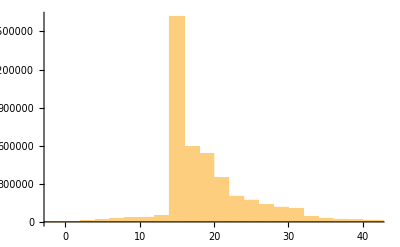

```mathematica
Histogram[Flatten[DeleteCases[tiemposHoutcome,"NA"|"Active"]//QuantityMagnitude]]
```

```mathematica
timeSoutcomeHUCI={"timeSoutcomeHUCI",Sequence@@(tiemposHoutcome/.{(x_/;MatchQ[x,Quantity[_,_]])->QuantityMagnitude[x],{"",DateObject[{2021,1,7},"Day","Gregorian",-5.]}->"NA"})};
```

```mathematica
(Length/@timeSoutcomeHUCI)//Tally
```

{{0,4874170}}

```mathematica
Select[timeSoutcomeHUCI,Length[#]==2&]
```

{{,Thu 7 Jan 2021}}

### variable 9

```mathematica
(*18. Desenlace hospitalización:0:No hospitalizado;1:Sí hospitalizado.*)
```

```mathematica
admitidosHUCI=(dataINSNew[[2;;,{15,21}]]//ToExpression)/.{({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->1,({x_,y_}/;MatchQ[x,DateObject[___]])->1,({x_,y_}/;MatchQ[y,DateObject[___]])->1,{Null,Null}->0};
```

```mathematica
admitidosHUCI//DeleteDuplicates
```

{0,1}

```mathematica
Transpose[{admitidosHUCI,outcome[[2;;]]}]//Tally
```

{{{0,Recovery},4503763},{{1,Recovery},195007},{{1,Deceased},53829},{{0,Deceased},69859},{{0,NA},8219},{{1,NA},6082},{{1,Active},16964},{{0,Active},20446}}

```mathematica
(*Aqui organizamos este outcome segun si son NA o casos Activos. Por ejemplo {0,"Active"} son casos que aún no se sabe si se hospitalizan, {1,"Active"} estos son casos que aunque no se sabe si se recuperan o mueren ya se sabe que  se hospitalizan *)
```

```mathematica
outcomeHUCI={"outcomeHUCI",Sequence@@(Transpose[{admitidosHUCI,outcome[[2;;]]}]/.{{0,"Recovery"}->0,{1,"Recovery"}->1,{1,"Deceased"}->1,{0,"Deceased"}->0,{0,"NA"}->"NA",{1,"NA"}->"NA",{1,"Active"}->1,{0,"Active"}->"Active"})};
```

```mathematica
outcomeHUCI//Tally
```

{{0,4573622},{1,265800},{NA,14301},{Active,20446}}

### variable 10

```mathematica
tiempos=Import["/home/lina/Documents/datos_INS/tiemposSRD.csv"]//ToExpression;
```

```mathematica
tiempos[[1;;6]]
```

{{15 days},{15 days},{15 days},{20 days},{15 days},{20 days}}

```mathematica
(*19. Tiempo de seguimiento desenlace ingreso UCI:(tiempo transcurrido desde la fecha de inicio de síntomas hasta la fecha de ingreso a UCI o hasta la fecha de recuperación o muerte (para los que no fueron ingresados a UCI)).*)
```

```mathematica
fechaAdmissionUCItiempos=Transpose[{fis2,dataINSNew[[2;;,21]]//ToExpression,tiempos}];
```

```mathematica
fechaAdmissionUCItiempos[[1]]
```

{Thu 27 Feb 2020,Null,{15 days}}

```mathematica
j=(dataINSNew[[2;;,21]]//ToExpression)/.(x_/;MatchQ[x,DateObject[___]])->date;
```

```mathematica
j//DeleteDuplicates
```

{Null,date}

```mathematica
fis2/.(x_/;MatchQ[x,DateObject[___]])->date;
```

```mathematica
%//DeleteDuplicates
```

{date,}

```mathematica
(*Identificando los tipos de combinaciones para construir las reglas en tiemposUCIoutcome *)
```

```mathematica
fechaAdmissionUCItiempos/.{({x_,y_,z_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->{date,date,t},({x_,y_,z_}/;MatchQ[x,DateObject[___]])->{date,y,t},({x_,y_,z_}/;MatchQ[y,DateObject[___]])->{x,date,t}};
```

```mathematica
%//DeleteDuplicates
```

{{date,Null,t},{,Null,NA},{date,date,t},{,date,t}}

```mathematica
tiemposUCIoutcome=fechaAdmissionUCItiempos/.{({x_,y_,z_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->QuantityMagnitude[y-x],({x_,Null,z_}/;MatchQ[x,DateObject[___]])->Sequence@@z,({"",y_,z_}/;MatchQ[y,DateObject[___]])->Sequence@@z,{"",Null,z_}->Sequence@@z};
```

```mathematica
(Length/@tiemposUCIoutcome)//Tally
```

{{2,4255471},{0,618698}}

```mathematica
Export["/home/lina/Documents/datos_INS/tiemposSUCI.csv",tiemposUCIoutcome]
```

/home/lina/Documents/datos_INS/tiemposSUCI.csv

```mathematica
DeleteCases[tiemposUCIoutcome,"NA"|"Active"]//QuantityMagnitude;
```

```mathematica
%[[1]]
```

{15}

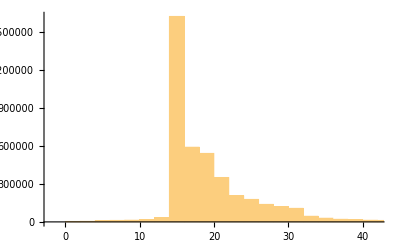

```mathematica
Histogram[Flatten[DeleteCases[tiemposUCIoutcome,"NA"|"Active"]//QuantityMagnitude]]
```

```mathematica
tiemposUCIoutcome[[1]]//QuantityMagnitude
```

{15}

```mathematica
tiemposSoutcomeUCI={"timeSoutcomeUCI",Sequence@@(tiemposUCIoutcome/.{(x_/;MatchQ[x,Quantity[_,_]])->QuantityMagnitude[x],{"",DateObject[{2021,1,7},"Day","Gregorian",-5.]}->"NA"})};
```

```mathematica
(Length/@tiemposSoutcomeUCI)//Tally
```

{{0,4874170}}

```mathematica
Histogram[tiemposSoutcomeUCI]
```

$Aborted

### variable 11

```mathematica
(*20. Desenlace ingreso UCI:0:No ingreso UCI;1:Sí ingreso UCI.*)
```

```mathematica
admitidosUCI=(dataINSNew[[2;;,21]]//ToExpression)/.{(x_/;MatchQ[x,DateObject[___]])->1,Null->0};
```

```mathematica
admitidosUCI//DeleteDuplicates
```

{0,1}

```mathematica
Transpose[{admitidosUCI,outcome[[2;;]]}]//Tally
```

{{{0,Recovery},4667604},{{1,Recovery},31166},{{1,Deceased},18881},{{0,Deceased},104807},{{0,NA},12830},{{1,NA},1471},{{0,Active},35724},{{1,Active},1686}}

```mathematica
(*Aqui organizamos este outcome segun si son NA o casos Activos. Por ejemplo {0,"Active"} son casos que aún no se sabe si entran a UCI, {1,"Active"} estos son casos que aunque no se sabe si se recuperan o mueren ya se sabe que entran a UCI *)
```

```mathematica
outcomeUCI={"outcomeUCI",Sequence@@(Transpose[{admitidosUCI,outcome[[2;;]]}]/.{{0,"Recovery"}->0,{1,"Recovery"}->1,{1,"Deceased"}->1,{0,"Deceased"}->0,{0,"NA"}->"NA",{1,"NA"}->"NA",{1,"Active"}->1,{0,"Active"}->"Active"})};
```

```mathematica
outcomeUCI//Tally
```

{{outcomeUCI,1},{0,4772411},{1,51733},{NA,14301},{Active,35724}}

{{0,4573622},{1,265800},{NA,14301},{Active,20446}}

### Building the data base

```mathematica
Length/@{{"ID",Sequence@@Range[1,Length[imp2019]-1]},imp2019,imp2020,ageYear,sexo,etnia,outcome,estado,tiemposFISoutcomeRD,outcomeD,outcomeR,timeSoutcomeHUCI,outcomeHUCI,tiemposSoutcomeUCI,outcomeUCI}
```

{4874170,4874170,4874170,4874170,4874170,4874170,4874170,4874170,4874170,4874170,4874170,4874170,4874170,4874170,4874170}

```mathematica
db=Transpose[{{"ID",Sequence@@Range[1,Length[imp2019]-1]},imp2019,imp2020,ageYear,sexo,etnia,outcome,estado,tiemposFISoutcomeRD,outcomeD,outcomeR,timeSoutcomeHUCI,outcomeHUCI,tiemposSoutcomeUCI,outcomeUCI}];
```

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseJP.csv",db]
```

/home/lina/Documents/datos_INS/dataBaseJP.csv

```mathematica
(*FALTA:
1. truncar los tiempos
2. hacer 2 data base por imp
3. describir las variables*)
```

```mathematica
db[[1;;3]]//Grid
```

ID | {IPM_DEP_2019,BLE_DEP_2019,BASS_DEP_2019,HC_DEP_2019,IEE_DEP_2019,SAFAM_DEP_2019,SAS_DEP_2019} | {IPM_DEP_2020,BLE_DEP_2020,BASS_DEP_2020,HC_DEP_2020,IEE_DEP_2020,SAFAM_DEP_2020,SAS_DEP_2020} | AgeYears | Gender | Ethnicity | outcomeRDA | state | timeSoutcomeRD | outcomeD | outcomeR | timeSoutcomeHUCI | outcomeHUCI | timeSoutcomeUCI | outcomeUCI
1 | {7.1,21.9,10.3,6.5,0.,0.1,13.5} | {7.5,23.3,2.9,6.4,0.5,0.6,16.9} | 19 | 0 | 6 | Recovery | 0 | 15 | 0 | 1 | 15 | 0 | 15 | 0
2 | {10.8,42.3,2.4,4.6,6.,4.9,9.9} | {11.1,34.9,1.2,4.4,3.,3.2,10.1} | 34 | 1 | 5 | Recovery | 1 | 15 | 0 | 1 | 11 | 1 | 15 | 0

```mathematica
db[[1]]//PositionIndex
```

<|ID→{1},{IPM_DEP_2019,BLE_DEP_2019,BASS_DEP_2019,HC_DEP_2019,IEE_DEP_2019,SAFAM_DEP_2019,SAS_DEP_2019}→{2},{IPM_DEP_2020,BLE_DEP_2020,BASS_DEP_2020,HC_DEP_2020,IEE_DEP_2020,SAFAM_DEP_2020,SAS_DEP_2020}→{3},AgeYears→{4},Gender→{5},Ethnicity→{6},outcomeRDA→{7},state→{8},timeSoutcomeRD→{9},outcomeD→{10},outcomeR→{11},timeSoutcomeHUCI→{12},outcomeHUCI→{13},timeSoutcomeUCI→{14},outcomeUCI→{15}|>

```mathematica
(*****************************************************************************adicionando IPM por municipio y *****************)
```

```mathematica
db=Import["/home/lina/Documents/datos_INS/dataBaseJP.csv"];
```

```mathematica
dbNew=Map[Flatten,Transpose[{db[[All,1;;3]],ipmMun2018,db[[All,4;;8]],tiemposFISoutcomeRD,db[[All,10;;15]]}]];
```

```mathematica
dbNew[[1;;3,10;;]]//Grid
```

SAS_TOT_MUN | AgeYears | Gender | Ethnicity | outcomeRDA | state | timeSoutcomeRD | outcomeD | outcomeR | timeSoutcomeHUCI | outcomeHUCI | timeSoutcomeUCI | outcomeUCI
18.7 | 19 | 0 | 6 | Recovery | 0 | 15 | 0 | 1 | 15 | 0 | 15 | 0
13.7 | 34 | 1 | 5 | Recovery | 1 | 15 | 0 | 1 | 11 | 1 | 15 | 0

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseJP.csv",dbNew];
```

```mathematica
(************************************************* ingresamos nuevamente la columna de tiempos: timeSoutcomeRD*)
```

```mathematica
db[[1]]//PositionIndex
```

<|ID→{1},{"IPM_DEP_2019", "BLE_DEP_2019", "BASS_DEP_2019", "HC_DEP_2019", "IEE_DEP_2019", "SAFAM_DEP_2019", "SAS_DEP_2019"}→{2},{"IPM_DEP_2020", "BLE_DEP_2020", "BASS_DEP_2020", "HC_DEP_2020", "IEE_DEP_2020", "SAFAM_DEP_2020", "SAS_DEP_2020"}→{3},IPM_MUN→{4},BLE_TOT_MUN→{5},BASS_TOT_MUN→{6},HC_TOT_MUN→{7},IEE_TOT_MUN→{8},SAFAM_TOT_MUN→{9},SAS_TOT_MUN→{10},AgeYears→{11},Gender→{12},Ethnicity→{13},outcomeRDA→{14},state→{15},timeSoutcomeRD→{16},outcomeD→{17},outcomeR→{18},timeSoutcomeHUCI→{19},outcomeHUCI→{20},timeSoutcomeUCI→{21},outcomeUCI→{22}|>

```mathematica
dbNew=Map[Flatten,Transpose[{db[[All,1;;15]],tiemposFISoutcomeRD,db[[All,17;;]]}]];
```

```mathematica
dbNew[[1]]
```

{ID,{"IPM_DEP_2019", "BLE_DEP_2019", "BASS_DEP_2019", "HC_DEP_2019", "IEE_DEP_2019", "SAFAM_DEP_2019", "SAS_DEP_2019"},{"IPM_DEP_2020", "BLE_DEP_2020", "BASS_DEP_2020", "HC_DEP_2020", "IEE_DEP_2020", "SAFAM_DEP_2020", "SAS_DEP_2020"},IPM_MUN,BLE_TOT_MUN,BASS_TOT_MUN,HC_TOT_MUN,IEE_TOT_MUN,SAFAM_TOT_MUN,SAS_TOT_MUN,AgeYears,Gender,Ethnicity,outcomeRDA,state,timeSoutcomeRD,outcomeD,outcomeR,timeSoutcomeHUCI,outcomeHUCI,timeSoutcomeUCI,outcomeUCI}

```mathematica
dbNew[[1;;3,10;;]]//Grid
```

SAS_TOT_MUN | AgeYears | Gender | Ethnicity | outcomeRDA | state | timeSoutcomeRD | outcomeD | outcomeR | timeSoutcomeHUCI | outcomeHUCI | timeSoutcomeUCI | outcomeUCI
18.7 | 19 | 0 | 6 | Recovery | 0 | 15 | 0 | 1 | 15 | 0 | 15 | 0
13.7 | 34 | 1 | 5 | Recovery | 1 | 15 | 0 | 1 | 11 | 1 | 15 | 0

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseJP.csv",dbNew];
```

```mathematica
Count[tiemposFISoutcomeRD,"NA"]
```

551826

```mathematica
db[[All,16]]==tiemposFISoutcomeRD
```

False

```mathematica
db[[All,16]][[1;;2]]
```

```mathematica
{"timeSoutcomeRD",15}
```

```mathematica
tiemposFISoutcomeRD[[1;;2]]
```

```mathematica
{"timeSoutcomeRD",15}
```

```mathematica
(*****************************************************Ingresamos el municipio*)
```

```mathematica
db=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseJP.csv"];
```

```mathematica
mun={"munName",Sequence@@(dataINSNew[[2;;,3]]/.rulesForNames)};(*Esto es algo que se habia hecho para poner el IPM por municipio: cambiar los nombres de algunos municipios para que quedaran como en el DANE*)
```

```mathematica
mun//Length
```

4874170

```mathematica
mun//Tally//Length
```

1036

```mathematica
newJP=Map[Flatten[#,1]&,Transpose[{db,mun}]];
```

```mathematica
db=newJP;
```

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseJP.csv",newJP]
```

/home/lina/Documents/UnCover/datos_INS/dataBaseJP.csv

```mathematica
newJP[[1;;3]]//Grid
```

ID | {"IPM_DEP_2019", "BLE_DEP_2019", "BASS_DEP_2019", "HC_DEP_2019", "IEE_DEP_2019", "SAFAM_DEP_2019", "SAS_DEP_2019"} | {"IPM_DEP_2020", "BLE_DEP_2020", "BASS_DEP_2020", "HC_DEP_2020", "IEE_DEP_2020", "SAFAM_DEP_2020", "SAS_DEP_2020"} | IPM_MUN | BLE_TOT_MUN | BASS_TOT_MUN | HC_TOT_MUN | IEE_TOT_MUN | SAFAM_TOT_MUN | SAS_TOT_MUN | AgeYears | Gender | Ethnicity | outcomeRDA | state | timeSoutcomeRD | outcomeD | outcomeR | timeSoutcomeHUCI | outcomeHUCI | timeSoutcomeUCI | outcomeUCI | munName
1 | {7.1, 21.9, 10.3, 6.5, 0., 0.1, 13.5} | {7.5, 23.3, 2.9, 6.4, 0.5, 0.6, 16.9} | 9. | 26.2 | 4.3 | 5.6 | 0.7 | 0.5 | 18.7 | 19 | 0 | 6 | Recovery | 0 | 15 | 0 | 1 | 15 | 0 | 15 | 0 | BOGOTA
2 | {10.8, 42.3, 2.4, 4.6, 6., 4.9, 9.9} | {11.1, 34.9, 1.2, 4.4, 3., 3.2, 10.1} | 12.3 | 40.9 | 4.2 | 4.8 | 1.1 | 1.6 | 13.7 | 34 | 1 | 5 | Recovery | 1 | 15 | 0 | 1 | 11 | 1 | 15 | 0 | BUGA

### Building a filtered database JP

```mathematica
db=Import["/home/lina/Documents/datos_INS/dataBaseJP.csv"];
```

```mathematica
db[[1]]//PositionIndex
```

<|ID→{1},{"IPM_DEP_2019", "BLE_DEP_2019", "BASS_DEP_2019", "HC_DEP_2019", "IEE_DEP_2019", "SAFAM_DEP_2019", "SAS_DEP_2019"}→{2},{"IPM_DEP_2020", "BLE_DEP_2020", "BASS_DEP_2020", "HC_DEP_2020", "IEE_DEP_2020", "SAFAM_DEP_2020", "SAS_DEP_2020"}→{3},IPM_MUN→{4},BLE_TOT_MUN→{5},BASS_TOT_MUN→{6},HC_TOT_MUN→{7},IEE_TOT_MUN→{8},SAFAM_TOT_MUN→{9},SAS_TOT_MUN→{10},AgeYears→{11},Gender→{12},Ethnicity→{13},outcomeRDA→{14},state→{15},timeSoutcomeRD→{16},outcomeD→{17},outcomeR→{18},timeSoutcomeHUCI→{19},outcomeHUCI→{20},timeSoutcomeUCI→{21},outcomeUCI→{22},munName→{23}|>

```mathematica
(*********************Eliminando IPMs DEP. Primero eliminar los dos casos que no match con el IPM_Mun)
```

```mathematica
Select[db,Length[#]<22&]
```

{{3749989,{66.5, 71.2, 1.8, 35.6, 72.6, 77., 1.9},{65.6, 60.7, 2.2, 31.1, 57.5, 69.3, 3.9},PAPUNAUA,33,0,6,Recovery,0,34,0,1,34,0,34,34},{4535145,{42.3, 63.4, 3.2, 9.3, 67.5, 67.5, 7.5},{49., 59.2, 1.3, 7.7, 66.7, 74.7, 5.4},BELEN DE BAJIRA,38,0,6,Active,1,Active,Active,Active,12,1,Active,Active}}

```mathematica
db1=DeleteCases[db,{3749989,"{66.5, 71.2, 1.8, 35.6, 72.6, 77., 1.9}","{65.6, 60.7, 2.2, 31.1, 57.5, 69.3, 3.9}","PAPUNAUA",33,0,6,"Recovery",0,34,0,1,34,0,34,34,"PAPUNAUA"}|{4535145,"{42.3, 63.4, 3.2, 9.3, 67.5, 67.5, 7.5}","{49., 59.2, 1.3, 7.7, 66.7, 74.7, 5.4}","BELEN DE BAJIRA",38,0,6,"Active",1,"Active","Active","Active",12,1,"Active","Active","BELEN DE BAJIRA"}];
```

```mathematica
Select[db1,Length[#]<22&]
```

{{3749989,{66.5, 71.2, 1.8, 35.6, 72.6, 77., 1.9},{65.6, 60.7, 2.2, 31.1, 57.5, 69.3, 3.9},PAPUNAUA,33,0,6,Recovery,0,34,0,1,34,0,34,34,PAPUNAUA},{4535145,{42.3, 63.4, 3.2, 9.3, 67.5, 67.5, 7.5},{49., 59.2, 1.3, 7.7, 66.7, 74.7, 5.4},BELEN DE BAJIRA,38,0,6,Active,1,Active,Active,Active,12,1,Active,Active,BELEN DE BAJIRA}}

```mathematica
{{3749989,"{66.5, 71.2, 1.8, 35.6, 72.6, 77., 1.9}","{65.6, 60.7, 2.2, 31.1, 57.5, 69.3, 3.9}","PAPUNAUA",33,0,6,"Recovery",0,34,0,1,34,0,34,34}}
```

```mathematica
db2=db1[[All,{1,Sequence@@Range[4,23]}]];
```

```mathematica
db2[[1]]//PositionIndex
```

<|ID→{1},IPM_MUN→{2},BLE_TOT_MUN→{3},BASS_TOT_MUN→{4},HC_TOT_MUN→{5},IEE_TOT_MUN→{6},SAFAM_TOT_MUN→{7},SAS_TOT_MUN→{8},AgeYears→{9},Gender→{10},Ethnicity→{11},outcomeRDA→{12},state→{13},timeSoutcomeRD→{14},outcomeD→{15},outcomeR→{16},timeSoutcomeHUCI→{17},outcomeHUCI→{18},timeSoutcomeUCI→{19},outcomeUCI→{20},munName→{21}|>

```mathematica
(*Eliminando NA en columna outcomeRDA que era columna Recuperado en la base original del INS. Esto se hace porque esos NAse son fallecidos por otras causas *)
```

```mathematica
Count[db2[[All,12]],"NA"]
```

14301

```mathematica
db3=DeleteCases[db2,{_,_,_,_,_,_,_,_,_,_,_,"NA",__}];
```

```mathematica
db3[[All,12]]//Tally
```

{{outcomeRDA,1},{Recovery,4698769},{Deceased,123688},{Active,37409}}

```mathematica
(* Eliminando NA, t>90, eliminar casos Activos / tomarlos como censurados contando los días desde FIS hasta 17/08/2021*)
```

```mathematica
Count[db[[All,16]],"NA"]
```

551826

```mathematica
Count[db3[[All,14]],"NA"]
```

537525

```mathematica
db4=DeleteCases[db3,{_,_,_,_,_,_,_,_,_,_,_,_,_,"NA"|"Active",__}];
```

```mathematica
Count[db4[[All,14]],"NA"]
```

0

```mathematica
Count[db4[[All,14]],"Active"]
```

0

```mathematica
(*************cuantos fallecidos queda?*)
```

```mathematica
(* outcome D*)
```

```mathematica
db4[[All,15]]//Tally
```

{{outcomeD,1},{0,4168682},{1,123688}}

```mathematica
(**************************************Eliminar la columna state porque tiene muchos NAs y muchas fuentes de ruido***)
```

```mathematica
neW=Map[Flatten,Transpose[{db4[[All,1;;12]],db4[[All,14;;]]}]];
```

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseJPcurada.csv",neW];
```

```mathematica
neW=Import["/home/lina/Documents/datos_INS/dataBaseJPcurada.csv"];
```

```mathematica
neW[[1]]//PositionIndex
```

<|ID→{1},IPM_MUN→{2},BLE_TOT_MUN→{3},BASS_TOT_MUN→{4},HC_TOT_MUN→{5},IEE_TOT_MUN→{6},SAFAM_TOT_MUN→{7},SAS_TOT_MUN→{8},AgeYears→{9},Gender→{10},Ethnicity→{11},outcomeRDA→{12},timeSoutcomeRD→{13},outcomeD→{14},outcomeR→{15},timeSoutcomeHUCI→{16},outcomeHUCI→{17},timeSoutcomeUCI→{18},outcomeUCI→{19},munName→{20}|>

```mathematica
(*********************************************quitando lo mayor a 120 en tiempos: timeSoutcomeRD*)
```

```mathematica
Select[neW,#[[13]]>90&]//Length
```

118675

```mathematica
Select[neW,#[[13]]>90&&#[[14]]==1&]//Length(*cuantos de los casos a eliminar son fallecidos?*)
```

1067

```mathematica
Select[neW,#[[13]]>100&]//Length
```

107978

```mathematica
Select[neW,#[[13]]>100&&#[[14]]==1&]//Length(*cuantos de los casos a eliminar son fallecidos?*)
```

921

```mathematica
Select[neW,#[[13]]>120&]//Length
```

86557

```mathematica
Select[neW,#[[13]]>120&&#[[14]]==1&]//Length(*cuantos de los casos a eliminar son fallecidos?*)
```

702

```mathematica
neW1=Select[neW,#[[13]]<=120&];
```

```mathematica
Length[neW]-Length[neW1]
```

86558

```mathematica
(*********************************************quitando lo mayor a 120 en tiempos: timeSoutcomeHUCI*)
```

```mathematica
Select[neW,#[[16]]>120&]//Length
```

71958

```mathematica
Select[neW,#[[16]]>120&&#[[17]]==1&]//Length(*cuantos de los casos a eliminar son hospitalizados?*)
```

8348

```mathematica
Select[neW1,#[[16]]>120&]//Length
```

7811

```mathematica
Select[neW1,#[[16]]>120&&#[[17]]==1&]//Length(*cuantos de los casos a eliminar son hospitalizados?*)
```

7811

```mathematica
Select[neW1,#[[16]]<120&]//Length(*cuantos de los casos a eliminar son hospitalizados?*)
```

4197149

```mathematica
Select[neW1,#[[16]]<120&&#[[17]]==1&]//Length(*cuantos de los casos a eliminar son hospitalizados?*)
```

212659

```mathematica
neW2=Select[neW1,#[[16]]<=120&];
```

```mathematica
Length[neW1]-Length[neW2]
```

7811

```mathematica
(*********************************************quitando lo mayor a 120 en tiempos: timeSoutcomeUCI*)
```

```mathematica
Select[neW2,#[[18]]>120&]//Length
```

90

```mathematica
Select[neW2,#[[18]]>120&&#[[19]]==1&]//Length(*cuantos de los casos a eliminar son fallecidos?*)
```

90

```mathematica
Select[neW2,#[[18]]<120&]//Length
```

4196990

```mathematica
Select[neW2,#[[18]]<120&&#[[19]]==1&]//Length
```

45427

```mathematica
neW3=Select[neW2,#[[18]]<=120&];
```

```mathematica
Length[neW2]-Length[neW3]
```

90

```mathematica
(***********************FINALMENTE cuantos muertos tenemos*)
```

```mathematica
Select[neW3,#[[14]]==1&]//Length
```

122757

```mathematica
Select[neW1,#[[14]]==1&]//Length
```

122986

```mathematica
(*******************************En esta dataBaseJPcurada2.csv se eliminan todos los tiempos (13,16,18) mayores a 120 días **)
```

```mathematica
neW3={neW[[1]],Sequence@@neW3};
```

```mathematica
neW3[[1]]
```

{ID,IPM_MUN,BLE_TOT_MUN,BASS_TOT_MUN,HC_TOT_MUN,IEE_TOT_MUN,SAFAM_TOT_MUN,SAS_TOT_MUN,AgeYears,Gender,Ethnicity,outcomeRDA,timeSoutcomeRD,outcomeD,outcomeR,timeSoutcomeHUCI,outcomeHUCI,timeSoutcomeUCI,outcomeUCI,munName}

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseJPcurada2.csv",neW3];
```

$Aborted

```mathematica
(*******************************En esta base eliminamos los indices que componen el IPM**)
```

```mathematica
sinTantosIndi=neW3[[All,{1,2,Sequence@@Range[9,20]}]];
```

```mathematica
sinTantosIndi[[1]]//Grid
```

Grid[{ID,IPM_MUN,AgeYears,Gender,Ethnicity,outcomeRDA,timeSoutcomeRD,outcomeD,outcomeR,timeSoutcomeHUCI,outcomeHUCI,timeSoutcomeUCI,outcomeUCI,munName}]

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseJPcurada3.csv",sinTantosIndi];
```

### Reviewing negatives values in times

```mathematica
(**************REVISANDO LOS NEGATIVOS EN timesSoutcomeHICU y timesSoutcomeHICU*)
```

```mathematica
(*La base dataINSNew es la base de las demas bases de datos y en secciones anteriores se revisó que estuviera bien la extracción de la info sobre hospitalización. Revisamos en esta las inconsistencias entre FIS y fecha de hospitalización*)
```

```mathematica
dataINSNew=Import["/home/lina/Documents/UnCover/datos_INS/dataINSNew.csv"];
```

```mathematica
dataINSNew[[1]]//PositionIndex
```

<|Caso→{1},Departamento_nom→{2},Ciudad_municipio_nom→{3},Edad→{4},unidad_medida→{5},Sexo→{6},per_etn_→{7},Ubicacion→{8},Estado→{9},Recuperado→{10},Fecha_inicio_sintomas→{11},Fecha_muerte→{12},Fecha_diagnostico→{13},Fecha_recuperado→{14},admissionH→{15},HRecovery→{16},HDeceased→{17},HUCI→{18},dischargeH→{19},timeHOutcomeRDT→{20},admissionUCI→{21},UCIRecovery→{22},UCIDeceased→{23},UCIH→{24},dischargeICU→{25},timeICUOutcomeRDT→{26}|>

```mathematica
(***************************************)
```

```mathematica
tiemposHoutcome=Import["/home/lina/Documents/UnCover/datos_INS/tiemposSH.csv"];(* contiene los tiempos desde FIS a H, ICU, o muerte/recuperacion *)
```

```mathematica
f["admissionH"]:="admissionH";
f[""]:="";
f[x_]:=ToExpression[x]
```

```mathematica
dataINSNew2=MapAt[f,dataINSNew,{All,15}];
```

```mathematica
tiemposHoutcome[[1]]
```

{15}

```mathematica
dataINSNew2[[1;;2]]//Grid
```

Caso | Departamento_nom | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | per_etn_ | Ubicacion | Estado | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
1 | BOGOTA | BOGOTA | 19 | 1 | F | 6 | Casa | Leve | Recuperado | 27/2/2020 0:00:00 |  | 6/3/2020 0:00:00 | 13/3/2020 0:00:00 |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
dataINSNew//Length
```

4874170

```mathematica
tiemposHoutcome//Length
```

4874169

```mathematica
posNEga=Position[tiemposHoutcome,_?Negative][[All,1]];
```

```mathematica
posNEga[[1;;5]]
```

{1764,2841,7618,12692,27804}

```mathematica
tiemposHoutcome[[1764]]
```

{-24}

```mathematica
Length[posNEga]
```

43

```mathematica
(**********el caso 1764 NO TIENE el match apropiado*)
```

```mathematica
dataINSNew[[{1,posNEga[[1]]+1}]]//Grid
```

Caso | Departamento_nom | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | per_etn_ | Ubicacion | Estado | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
1764 | BARRANQUILLA | BARRANQUILLA | 6 | 1 | F | 6 | Casa | Leve | Recuperado | 1/5/2020 0:00:00 |  |  | 26/10/2020 0:00:00 | Tue 7 Apr 2020 | DateObject[{2020, 4, 8}, "Day", "Gregorian", -5.] |  |  | DateObject[{2020, 4, 8}, "Day", "Gregorian", -5.] | Quantity[1, "Days"] |  |  |  |  | Missing | Missing

```mathematica
caso=Import["/home/lina/Documents/UnCover/datos_INS/2020-04-07.xlsx"];
```

```mathematica
caso[[1,{1,posNEga[[1]]+1}]]//Grid
```

Caso | Fecha Not | Departamento | Ciudad | Edad | Sexo | Tipo | Ubicación | Estado | Pais de procedencia | Fecha de inicio de síntomas
1764. | Fri 27 Mar 2020 00:00:00GMT-5 | Valle del Cauca | Cali | 58. | F | En estudio | Hospital | Moderado | Colombia | Fri 20 Mar 2020 00:00:00GMT-5

```mathematica
(**********el casos 2841 NO TIENE el match apropiado*)
```

```mathematica
dataINSNew2[[{1,posNEga[[2]]+1}]]//Grid
```

Caso | Departamento_nom | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | per_etn_ | Ubicacion | Estado | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
2841 | BARRANQUILLA | BARRANQUILLA | 17 | 1 | F | 6 | Casa | Leve | Recuperado | 10/9/2020 0:00:00 |  | 10/9/2020 0:00:00 | 28/9/2020 0:00:00 | Mon 13 Apr 2020 | DateObject[{2020, 4, 23}, "Day", "Gregorian", -5.] |  |  | DateObject[{2020, 4, 23}, "Day", "Gregorian", -5.] | Quantity[10, "Days"] |  |  |  |  | Missing | Missing

```mathematica
caso=Import["/home/lina/Documents/UnCover/datos_INS/2020-04-13.xlsx"];
```

```mathematica
caso[[1,posNEga[[2]]+1]]//Grid
```

Grid[{2841.,Sat 11 Apr 2020 00:00:00GMT-5,VALLE,CALI,70.,M,En estudio,Hospital,Moderado,COLOMBIA,,Sat 29 Feb 2020 00:00:00GMT-5,  -   -}]

```mathematica
(**********el casos 2840 (que no es negativo en timesSH) SI TIENE el match apropiado*)
```

```mathematica
dataINSNew2[[{1,posNEga[[2]]}]]//Grid
```

Caso | Departamento_nom | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | per_etn_ | Ubicacion | Estado | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
2840 | VALLE | CALI | 72 | 1 | M | 6 | Casa | Leve | Recuperado | 2/4/2020 0:00:00 |  | 13/4/2020 0:00:00 | 13/5/2020 0:00:00 | Mon 13 Apr 2020 |  |  | DateObject[{2020, 4, 23}, "Day", "Gregorian", -5.] | DateObject[{2020, 4, 23}, "Day", "Gregorian", -5.] | Quantity[10, "Days"] | DateObject[{2020, 4, 23}, "Day", "Gregorian", -5.] | DateObject[{2020, 5, 3}, "Day", "Gregorian", -5.] |  |  | DateObject[{2020, 5, 3}, "Day", "Gregorian", -5.] | Quantity[10, "Days"]

```mathematica
caso[[1,posNEga[[2]]]]//Grid
```

Grid[{2840.,Sat 11 Apr 2020 00:00:00GMT-5,VALLE,CALI,72.,M,En estudio,Hospital,Moderado,COLOMBIA,,Thu 2 Apr 2020 00:00:00GMT-5,  -   -}]

```mathematica
(**********el casos 2838 SI TIENE el match apropiado*)
```

```mathematica
dataINSNew2[[{1,posNEga[[2]]-2}]]//Grid
```

Caso | Departamento_nom | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | per_etn_ | Ubicacion | Estado | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | admissionH | HRecovery | HDeceased | HUCI | dischargeH | timeHOutcomeRDT | admissionUCI | UCIRecovery | UCIDeceased | UCIH | dischargeICU | timeICUOutcomeRDT
2838 | VALLE | CALI | 41 | 1 | M | 6 | Casa | Leve | Recuperado | 4/4/2020 0:00:00 |  | 13/4/2020 0:00:00 | 31/5/2020 0:00:00 | Mon 11 May 2020 | DateObject[{2020, 5, 31}, "Day", "Gregorian", -5.] |  |  | DateObject[{2020, 5, 31}, "Day", "Gregorian", -5.] | Quantity[20, "Days"] | DateObject[{2020, 4, 13}, "Day", "Gregorian", -5.] |  |  | DateObject[{2020, 5, 11}, "Day", "Gregorian", -5.] | DateObject[{2020, 5, 11}, "Day", "Gregorian", -5.] | Quantity[28, "Days"]

```mathematica
caso[[1,posNEga[[2]]-2]]//Grid
```

Grid[{2838.,Sat 11 Apr 2020 00:00:00GMT-5,VALLE,CALI,41.,M,En estudio,Hospital UCI ,Grave,COLOMBIA,,Sat 4 Apr 2020 00:00:00GMT-5,  -   -}]

```mathematica
(*****************CONCLUSIÓN : Hay casos que no tienen un match apropiado entre las bases del datos del INS y las fechas estimadas de hospitalización. Vamos a revisar cuales son esos casos*)
```

```mathematica
dataINS=Import["/home/lina/Documents/UnCover/datos_INS/2021-08-17.csv"];
```

```mathematica
dataINS[[1]]//PositionIndex
```

<|fecha_hoy_casos→{1},Caso→{2},Fecha Not→{3},Departamento→{4},Departamento_nom→{5},Ciudad_municipio→{6},Ciudad_municipio_nom→{7},Edad→{8},unidad_medida→{9},Sexo→{10},Fuente_tipo_contagio→{11},Ubicacion→{12},Estado→{13},Pais_viajo_1_cod→{14},Pais_viajo_1_nom→{15},Recuperado→{16},Fecha_inicio_sintomas→{17},Fecha_muerte→{18},Fecha_diagnostico→{19},Fecha_recuperado→{20},Tipo_recuperacion→{21},per_etn_→{22},nom_grupo_→{23}|>

```mathematica
dataINS//Length
```

4874170

```mathematica
dataINSNew//Length
```

4874170

```mathematica
(dataINS[[2;;,8]]-dataINSNew[[2;;,4]])//Tally
```

{{0,4874169}}

```mathematica
Position[dataINS[[2;;,8]]-dataINSNew[[2;;,4]],x_/;x!=0];
```

```mathematica
%//Length
```

0

```mathematica
dataINS[[posNEga[[1]]+1]]
```

{8/4/2020 0:00:00,1764,4/5/2020 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,6,1,F,Comunitaria,Casa,Leve,,,Recuperado,1/5/2020 0:00:00,,,26/10/2020 0:00:00,Tiempo,6,}

```mathematica
dataINSNew[[posNEga[[1]]+1]]
```

{1764,BARRANQUILLA,BARRANQUILLA,6,1,F,6,Casa,Leve,Recuperado,1/5/2020 0:00:00,,,26/10/2020 0:00:00,DateObject[{2020, 4, 7}, "Day", "Gregorian", -5.],DateObject[{2020, 4, 8}, "Day", "Gregorian", -5.],,,DateObject[{2020, 4, 8}, "Day", "Gregorian", -5.],Quantity[1, "Days"],,,,,Missing,Missing}

```mathematica
dataINSNew[[#+1,{1,2,3,4,6}]]==dataINS[[#+1,{2,5,7,8,10}]]&/@posNEga
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* CONCLUSIÓN: los datos de los casos entre estas bases de datos match perfectamente. Entonces los errores en timesSH es porque en bases de datos del INS se consigna mal la informacion y se cambian la posicion de los casos y por tal motivo el codigo para restrear las fechas de ingresos los tomó mal. LA SOLUCION es eliminar los casos negativos *)
```

```mathematica
data1=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseJPcurada3.csv"];
```

```mathematica
data1//Length
```

4197913

```mathematica
data1[[1]]//PositionIndex
```

<|ID→{1},IPM_MUN→{2},AgeYears→{3},Gender→{4},Ethnicity→{5},outcomeRDA→{6},timeSoutcomeRD→{7},outcomeD→{8},outcomeR→{9},timeSoutcomeHUCI→{10},outcomeHUCI→{11},timeSoutcomeUCI→{12},outcomeUCI→{13},munName→{14}|>

```mathematica
Count[data1[[2;;,10]],_?Negative]
```

40

```mathematica
Count[data1[[2;;,10]],0]
```

1591

```mathematica
Count[data1[[2;;,12]],_?Negative]
```

6

```mathematica
data2=Select[data1,#[[10]]>1&&#[[12]]>1&];
```

```mathematica
data2//Length
```

4195909

```mathematica
%61-%67(*Al menos 46 casos se eliminaron por ser negativos , los demas por ser 0*)
```

3357

```mathematica
(**********************************************)
```

```mathematica
data3={data1[[1]],Sequence@@data2};
```

```mathematica
data3//Length
```

4195910

```mathematica
data3[[1]]//PositionIndex
```

<|ID→{1},IPM_MUN→{2},AgeYears→{3},Gender→{4},Ethnicity→{5},outcomeRDA→{6},timeSoutcomeRD→{7},outcomeD→{8},outcomeR→{9},timeSoutcomeHUCI→{10},outcomeHUCI→{11},timeSoutcomeUCI→{12},outcomeUCI→{13},munName→{14}|>

```mathematica
Count[data3[[2;;,12]],_?Negative]
```

0

```mathematica
Count[data3[[2;;,10]],_?Negative]
```

0

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseJPcurada4.csv",data3];
```

### DataBase for the multilevel analysis

This database is for the multi-level analysis

```mathematica
data3=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseJPcurada4.csv"];
```

```mathematica
dataNew=Import["/home/lina/Documents/UnCover/datos_INS/BD_unCover_Covariables.xlsx"];
```

```mathematica
data3[[1]]//PositionIndex
```

<|ID→{1},IPM_MUN→{2},AgeYears→{3},Gender→{4},Ethnicity→{5},outcomeRDA→{6},timeSoutcomeRD→{7},outcomeD→{8},outcomeR→{9},timeSoutcomeHUCI→{10},outcomeHUCI→{11},timeSoutcomeUCI→{12},outcomeUCI→{13},munName→{14}|>

```mathematica
dataNew//Dimensions
```

{1,1123,12}

```mathematica
dataNew[[1,1;;4]]//Grid
```

COD_DEP | DEP_NOM | COD_MUN_DANE | COD_MUN_INS | MUN_NOM | IPM_MUN | PRE_HTA | PRE_DM | PRE_ERC | PRE_CA | POB_DANE | DEB_POB
91 | AMAZONAS | 91263. | 91263. | EL ENCANTO | 77.5 | 0. | 0. | 0. | 0. | 2077. | 0.19055
91 | AMAZONAS | 91405. | 91405. | LA CHORRERA (CD) | 88.1 | 0. | 0. | 0. | 0. | 2955. | 0.232138
91 | AMAZONAS | 91407. | 91407. | LA PEDRERA (CD) | 90.9 | 0.11 | 0. | 0. | 2443.93 | 3947. | 0.288267

```mathematica
(******************************************************************************)
```

```mathematica
rulesDataNew=Thread[dataNew[[1,2;;All,5]]->dataNew[[1,2;;All,6;;-1]]];
```

```mathematica
nombreMdataNew=dataNew[[1,2;;All,5]];
```

```mathematica
nombreMdata3=data3[[2;;,14]]//DeleteDuplicates;
```

```mathematica
Sort[nombreMdataNew]==Sort[nombreMdata3]
```

False

```mathematica
Complement[nombreMdataNew,nombreMdata3]
```

{LA GUADALUPE,MIRITI - PARANA,MORICHAL,PAPUNAHUA,PUERTO ALEGRIA,VILLARRICA}

```mathematica
Complement[nombreMdata3,nombreMdataNew]
```

{}

```mathematica
newVar=data3[[2;;,14]]/.rulesDataNew;
```

```mathematica
Select[newVar,Length[#]<2&]
```

{}

```mathematica
codigoM=data3[[2;;,14]]/.Thread[dataNew[[1,2;;All,5]]->dataNew[[1,2;;All,4]]];
```

```mathematica
data4={{"ID","CodeM","nameM","Age","Gender","Ethnicity","times","statusD","statusR","IPM_MUN","PRE_HTA","PRE_DM","PRE_ERC","PRE_CA","POB_DANE","DEN_POB"},Sequence@@Map[Flatten[#,1]&,Transpose[{Range[1,Length[data3]-1],codigoM,data3[[2;;,{14,3,4,5,7,8,9}]],newVar}]]};
```

```mathematica
data4[[1;;3]]//Grid
```

ID | CodeM | nameM | Age | Gender | Ethnicity | times | statusD | statusR | IPM_MUN | PRE_HTA | PRE_DM | PRE_ERC | PRE_CA | POB_DANE | DEN_POB
1 | 11001. | BOGOTA | 19 | 0 | 6 | 15 | 0 | 1 | 9. | 10.55 | 3.46 | 2.64 | 1516.76 | 7.74396×10^6 | 4774.68
2 | 76111. | BUGA | 34 | 1 | 5 | 15 | 0 | 1 | 12.3 | 13.82 | 5.17 | 2.75 | 451.7 | 128945. | 156.394

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseJPcurada5.csv",data4];
```

### DataBase for Competing Risk Model

```mathematica
data5=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseJPcurada5.csv"];
```

```mathematica
data5[[1]]//PositionIndex
```

<|ID→{1},CodeM→{2},nameM→{3},Age→{4},Gender→{5},Ethnicity→{6},times→{7},statusD→{8},statusR→{9},IPM_MUN→{10},PRE_HTA→{11},PRE_DM→{12},PRE_ERC→{13},PRE_CA→{14},POB_DANE→{15},DEN_POB→{16}|>

```mathematica
data5[[2;;,{8,9}]]//Tally
```

{{{0,1},4075011},{{1,0},119545}}

```mathematica
rules={{id_,age_,sex_,t_,1,0}->{{id,t,1,1,"D",age,sex},{id,t,0,2,"R",age,sex}},{id_,age_,sex_,t_,0,1}->{{id,t,0,1,"D",age,sex},{id,t,1,2,"R",age,sex}}};
```

```mathematica
data6={{"ID","times","status","stratum","cause","Age","Gender"},Sequence@@Flatten[data5[[2;;,{1,4,5,7,8,9}]]/.rules,1]};
```

```mathematica
data6[[1;;3]]//Grid
```

ID | times | status | stratum | cause | Age | Gender
1 | 15 | 0 | 1 | D | 19 | 0
1 | 15 | 1 | 2 | R | 19 | 0

```mathematica
Export["/home/lina/Documents/UnCover/datos_INS/dataBaseJPcurada6.csv",data6];
```